## Initial stuff

```mathematica
Clear["Global`*"]
```

```mathematica
H=({{ω0, (ωp ⅇ^(ⅈ ϕ))/(√2), 0}, {(ωp ⅇ^(-ⅈ ϕ))/(√2), 0, (ωp ⅇ^(ⅈ ϕ))/(√2)}, {0, (ωp ⅇ^(-ⅈ ϕ))/(√2), -ω0}});
```

```mathematica
{eval,evec}=Eigensystem[H];
```

```mathematica
evec//FullSimplify//MatrixForm
```

(-ⅇ^(2 ⅈ ϕ) | (√2 ⅇ^(ⅈ ϕ) ω0)/ωp | 1
(ⅇ^(2 ⅈ ϕ) (ωp^2+2 ω0 (ω0-√(ω0^2+ωp^2))))/ωp^2 | (√2 ⅇ^(ⅈ ϕ) (ω0-√(ω0^2+ωp^2)))/ωp | 1
(ⅇ^(2 ⅈ ϕ) (ωp^2+2 ω0 (ω0+√(ω0^2+ωp^2))))/ωp^2 | (√2 ⅇ^(ⅈ ϕ) (ω0+√(ω0^2+ωp^2)))/ωp | 1)

```mathematica
eval
```

{0,-√(ω0^2+ωp^2),√(ω0^2+ωp^2)}

```mathematica
Hnew = ({{ω0, (ωp ⅇ^(ⅈ ϕ))/(√2), 0}, {(ωp ⅇ^(-ⅈ ϕ))/(√2), 0, (ωp ⅇ^(ⅈ ϕ))/(√2)}, {0, (ωp ⅇ^(-ⅈ ϕ))/(√2), -ω0}})/.ω0->0;
```

```mathematica
Eigenvalues[Hnew]
```

{0,-ωp,ωp}

```mathematica
Eigenvectors[Hnew]
```

{{-ⅇ^(2 ⅈ ϕ),0,1},{ⅇ^(2 ⅈ ϕ),-√2 ⅇ^(ⅈ ϕ),1},{ⅇ^(2 ⅈ ϕ),√2 ⅇ^(ⅈ ϕ),1}}

```mathematica
(*λ = 0*)evec[[1]] *(q ⅇ^(-ⅈ ϕ))/(√2)ωp//FullSimplify//MatrixForm
```

(-(ⅇ^(ⅈ ϕ) q ωp)/(√2)
q ω0
(ⅇ^(-ⅈ ϕ) q ωp)/(√2))

```mathematica
(*λ = -√(ω0^2+ωp^2)*)evec[[2]]*(q ⅇ^(-ⅈ ϕ))/(√2)(√(ω0^2+ωp^2)+ω0)//FullSimplify//MatrixForm
```

((ⅇ^(ⅈ ϕ) q (-ω0+√(ω0^2+ωp^2)))/(√2)
-q ωp
(ⅇ^(-ⅈ ϕ) q (ω0+√(ω0^2+ωp^2)))/(√2))

```mathematica
(*λ = √(ω0^2+ωp^2)*)evec[[3]]*(q ⅇ^(-ⅈ ϕ))/(√2)(√(ω0^2+ωp^2)-ω0)//FullSimplify//MatrixForm
```

((ⅇ^(ⅈ ϕ) q (ω0+√(ω0^2+ωp^2)))/(√2)
q ωp
(ⅇ^(-ⅈ ϕ) q (-ω0+√(ω0^2+ωp^2)))/(√2))

```mathematica
a=ω0;b=√(ω0^2+ωp^2);
```

```mathematica
(a-b)(a+b)//Expand
```

-ωp^2

```mathematica
ψ0=({{(-q ⅇ^(ⅈ ϕ))/(√2)ωp}, {q ω0}, {(q ⅇ^(-ⅈ ϕ))/(√2)ωp}});ψp=({{(q ⅇ^(ⅈ ϕ))/(√2)(√(ω0^2+ωp^2)+ω0)}, {q ωp}, {(q ⅇ^(-ⅈ ϕ))/(√2)(√(ω0^2+ωp^2)-ω0)}});ψm=({{(q ⅇ^(ⅈ ϕ))/(√2)(√(ω0^2+ωp^2)-ω0)}, {-q ωp}, {(q ⅇ^(-ⅈ ϕ))/(√2)(√(ω0^2+ωp^2)+ω0)}});
```

```mathematica
λ0=0;λp=√(ω0^2+ωp^2);λm=-√(ω0^2+ωp^2);
```

```mathematica
H.ψ0==λ0 ψ0//FullSimplify
```

True

```mathematica
H.ψp==λp ψp//FullSimplify
```

True

```mathematica
H.ψm==λm ψm//FullSimplify
```

True

```mathematica
Assuming[{q,ω0,ωp,ϕ}∈Reals,Normalize[ψpᵀ[[1]]]]//ComplexExpand//PowerExpand//FullSimplify
```

{(ⅇ^(ⅈ ϕ) q (ω0+√(ω0^2+ωp^2)))/(2 √(q^2 (ω0^2+ωp^2))),(q ωp)/(√2 √(q^2 (ω0^2+ωp^2))),(ⅇ^(-ⅈ ϕ) q (-ω0+√(ω0^2+ωp^2)))/(2 √(q^2 (ω0^2+ωp^2)))}

```mathematica
J=({{(j ⅇ^(ⅈ Ψ))/(√2)}, {(ρ ωp)/q}, {(j ⅇ^(-ⅈ Ψ))/(√2)}});
```

```mathematica
Normalize[ψpᵀ[[1]]]//ComplexExpand//FullSimplify
```

{(ⅇ^(ⅈ ϕ) q (ω0+√(ω0^2+ωp^2)))/(2 √(q^2 (ω0^2+ωp^2))),(q ωp)/(√2 √(q^2 (ω0^2+ωp^2))),(ⅇ^(-ⅈ ϕ) q (-ω0+√(ω0^2+ωp^2)))/(2 √(q^2 (ω0^2+ωp^2)))}

```mathematica
Solve[(q ωp)/(√2 √(q^2 (ω0^2+ωp^2)))==(ρ ωp)/q]//ComplexExpand//FullSimplify
```

{{ρ→(√(q^2))/(√2 √(ω0^2+ωp^2))},{ωp→0}}

```mathematica
ω0=u q (*at long range*)
```

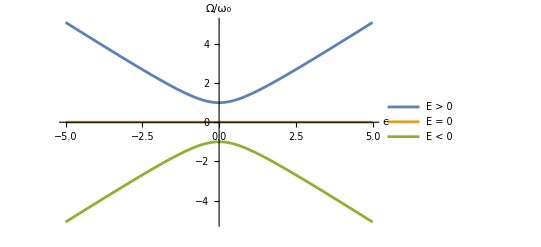

```mathematica
plt=Plot[{√(ϵ^2+1),0,-√(ϵ^2+1)},{ϵ,-5,5},AxesLabel->{ϵ,Ω/Subscript[ω, 0]},PlotLegends->{"E > 0","E = 0","E < 0"}]
```

```mathematica
Export["Test.pdf",plt]
```

Test.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Test.png"]]]
```

```mathematica
Solve[{1/(√2)(jx+ⅈ jy)==(q ⅇ^(ⅈ ϕ))/(√2)(λ+ω0),1/(√2)(jx-ⅈ jy)==(q ⅇ^(-ⅈ ϕ))/(√2)(λ-ω0)},{jx,jy}]//FullSimplify
```

{{jx→q (λ Cos[ϕ]+ⅈ ω0 Sin[ϕ]),jy→q (-ⅈ ω0 Cos[ϕ]+λ Sin[ϕ])}}

```mathematica
H=({{-ω0, ωp/(√2)ⅇ^(ⅈ ϕ), 0}, {ωp/(√2)μ^2 ⅇ^(-ⅈ ϕ), 0, ωp/(√2)μ^2 ⅇ^(ⅈ ϕ)}, {0, ωp/(√2)ⅇ^(-ⅈ ϕ), ω0}});
```

```mathematica
Eigenvalues[H]
```

{0,-√(ω0^2+μ^2 ωp^2),√(ω0^2+μ^2 ωp^2)}

```mathematica
Eigenvectors[H]//FullSimplify
```

{{-ⅇ^(2 ⅈ ϕ),-(√2 ⅇ^(ⅈ ϕ) ω0)/ωp,1},{ⅇ^(2 ⅈ ϕ) (1+(2 ω0 (ω0+√(ω0^2+μ^2 ωp^2)))/(μ^2 ωp^2)),-(√2 ⅇ^(ⅈ ϕ) (ω0+√(ω0^2+μ^2 ωp^2)))/ωp,1},{ⅇ^(2 ⅈ ϕ) (1+(2 ω0 (ω0-√(ω0^2+μ^2 ωp^2)))/(μ^2 ωp^2)),(√2 ⅇ^(ⅈ ϕ) (-ω0+√(ω0^2+μ^2 ωp^2)))/ωp,1}}

```mathematica
{ⅇ^(2 ⅈ ϕ) (1+(2 ω0 (ω0-√(ω0^2+μ^2 ωp^2)))/(μ^2 ωp^2)),(√2 ⅇ^(ⅈ ϕ) (-ω0+√(ω0^2+μ^2 ωp^2)))/ωp,1}*ⅇ^(-ⅈ ϕ)(ω0+√(ω0^2+μ^2 ωp^2))//ComplexExpand//FullSimplify
```

{ⅇ^(ⅈ ϕ) (-ω0+√(ω0^2+μ^2 ωp^2)),√2 μ^2 ωp,ⅇ^(-ⅈ ϕ) (ω0+√(ω0^2+μ^2 ωp^2))}

```mathematica
Normalize[{ⅇ^(ⅈ ϕ) (-ω0+√(ω0^2+μ^2 ωp^2)),√2 μ^2 ωp,ⅇ^(-ⅈ ϕ) (ω0+√(ω0^2+μ^2 ωp^2))}]//ComplexExpand//FullSimplify
```

{(ⅇ^(ⅈ ϕ) (-ω0+√(ω0^2+μ^2 ωp^2)))/(√(4 ω0^2+2 μ^2 (1+μ^2) ωp^2)),(μ^2 ωp)/(√(2 ω0^2+μ^2 (1+μ^2) ωp^2)),(ⅇ^(-ⅈ ϕ) (ω0+√(ω0^2+μ^2 ωp^2)))/(√(4 ω0^2+2 μ^2 (1+μ^2) ωp^2))}

```mathematica
Manipulate[Plot[{-√(1+ρfrac*x^2),√(1+ρfrac*x^2),0},{x,-5,5},PlotRange->{0,5}],{ρfrac,0,2}]
```

```mathematica
Energy[ϵ_,μ_]:=√(1+μ ϵ^2)
```

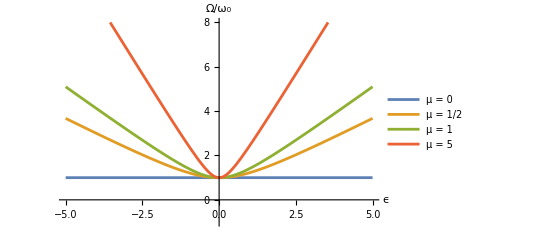

```mathematica
nrgplt = Plot[{Energy[ϵ,0],Energy[ϵ,1/2],Energy[ϵ,1],Energy[ϵ,5]},{ϵ,-5,5},PlotRange->{-1,8},PlotLegends->{"μ = 0", "μ = 1/2","μ = 1", "μ = 5"},AxesLabel->{"ϵ","Ω/ω_0"}]
```

```mathematica
Export["energyplot.pdf",nrgplt]
```

energyplot.pdf

```mathematica
Directory[]
```

C:\Users\sokws

## Scattering problem, step potential

```mathematica
R =((q-qp)/(q+qp))^2/.{q->ω/u,qp->(√(ω^2-ω0^2))/u}//FullSimplify
```

((ω-√(ω^2-ω0^2))^2)/((ω+√(ω^2-ω0^2))^2)

```mathematica
T = (4q qp)/(q+qp)^2/.{q->ω/u,qp->(√(ω^2-ω0^2))/u}//FullSimplify
```

(4 ω √((ω-ω0) (ω+ω0)))/((ω+√(ω^2-ω0^2))^2)

```mathematica
R+T//FullSimplify
```

1

```mathematica
((ω-√(ω^2-ω0^2))^2)/((ω+√(ω^2-ω0^2))^2)/.ω->ϵ ω0//FullSimplify
```

((-ϵ ω0+√((-1+ϵ^2) ω0^2))^2)/((ϵ ω0+√((-1+ϵ^2) ω0^2))^2)

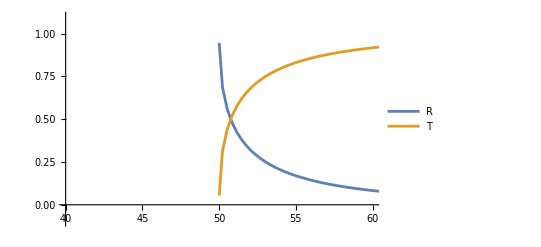

```mathematica
With[{ω0=50},Plot[{((ω-√(ω^2-ω0^2))^2)/((ω+√(ω^2-ω0^2))^2),(4 ω √(ω^2-ω0^2))/((ω+√(ω^2-ω0^2))^2)},{ω,0,1000},PlotRange->{{40,60},{-0.1,1.1}},PlotLegends->{"R","T"}]]
```

```mathematica
Clear["Global`*"]
```

```mathematica
R[ϵ_]:=((ϵ-√(ϵ^2-1))^2)/((ϵ+√(ϵ^2-1))^2);T[ϵ_]:=(4ϵ √(ϵ^2-1))/((ϵ+√(ϵ^2-1))^2);
```

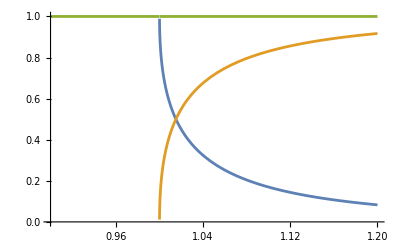

```mathematica
Plot[{R[ϵ],T[ϵ],R[ϵ]+T[ϵ]},{ϵ,0.9,1.2}]
```

## Step potential but goes down - tunneling

```mathematica
(4(qp/q)^2)/((1-qp^2/q^2)^2 Sinh[qp r]^2+4(qp/q)^2 Cosh[qp r]^2)/.{q->ω/u,qp->(√(ω0^2-ω^2))/u}/.ω->ϵ ω0//FullSimplify
```

(8 ϵ^2 (-1+ϵ^2))/(1-8 ϵ^2+8 ϵ^4-Cos[(2 r √(-1+ϵ^2) ω0)/u])

```mathematica
Assuming[ϵ<1,FullSimplify[(8 ϵ^2 (-1+ϵ^2))/(1-8 ϵ^2+8 ϵ^4-Cos[(2 r  ⅈ √(1-ϵ^2) ω0)/u])]]
```

(8 ϵ^2 (-1+ϵ^2))/(1-8 ϵ^2+8 ϵ^4-Cosh[(2 r √(1-ϵ^2) ω0)/u])

```mathematica
Limit[(8 ϵ^2 (-1+ϵ^2))/(1-8 ϵ^2+8 ϵ^4-Cosh[(2 r √(1-ϵ^2) ω0)/u]),r->∞]
```

ConditionalExpression[0, u √(1-ϵ^2) ω0>0]

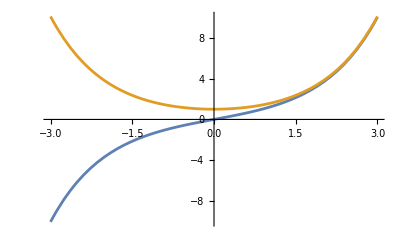

```mathematica
Plot[{Sinh[x],Cosh[x]},{x,-3,3}]
```

```mathematica
((4 qp / q)/(1+(qp/q)^2))^2/.{q->ω/u,qp->(√(ω0^2-ω^2))/u}/.ω->ϵ ω0//FullSimplify//Expand
```

16 ϵ^2-16 ϵ^4

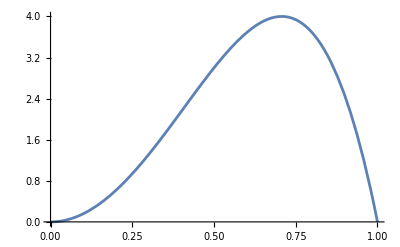

```mathematica
Plot[16 ϵ^2-16 ϵ^4,{ϵ,0,1}]
```

```mathematica
(√(ω0^2-ω^2))/u/.ω->ϵ ω0
```

(√(ω0^2-ϵ^2 ω0^2))/u

```mathematica
Clear["Global`*"]
```

```mathematica
ψ1[x_]:=a ⅇ^(ⅈ q x)+a b ⅇ^(-ⅈ q x);ψ2[x_]:=a c ⅇ^(-qp x)+a d ⅇ^(qp x);ψ3[x_]:=a f ⅇ^(ⅈ q x)
```

```mathematica
Solve[{ψ1[0]==ψ2[0],ψ1'[0]==ψ2'[0],ψ2[r]==ψ3[r],ψ2'[r]==ψ3'[r]},{b,c,d,f}]//FullSimplify
```

{{b→((q^2+qp^2) Sinh[qp r])/(2 ⅈ q qp Cosh[qp r]+(q-qp) (q+qp) Sinh[qp r]),c→(2 ⅇ^(2 qp r) q (q+ⅈ qp))/(-(q-ⅈ qp)^2+ⅇ^(2 qp r) (q+ⅈ qp)^2),d→-(2 q (q-ⅈ qp))/(-(q-ⅈ qp)^2+ⅇ^(2 qp r) (q+ⅈ qp)^2),f→(2 ⅈ ⅇ^(-ⅈ q r) q qp)/(2 ⅈ q qp Cosh[qp r]+(q-qp) (q+qp) Sinh[qp r])}}

```mathematica
Assuming[{q,qp}∈Reals,FullSimplify[Abs[(2 ⅈ ⅇ^(-ⅈ q r) q qp)/(2 ⅈ q qp Cosh[qp r]+(q-qp) (q+qp) Sinh[qp r])]^2]]//ComplexExpand
```

(4 q^2 qp^2)/(4 q^2 qp^2 Cosh[qp r]^2+(q-qp)^2 (q+qp)^2 Sinh[qp r]^2)

```mathematica
((q-qp)^2 (q+qp)^2)/q^4==(1-qp^2/q^2)^2//Expand
```

True

## Step potential but goes down - no tunneling

```mathematica
Clear["Global`*"]
```

```mathematica
ψ1[x_]:=a ⅇ^(ⅈ q x)+a b ⅇ^(-ⅈ q x);ψ2[x_]:=a c ⅇ^(ⅈ qp x)+a d ⅇ^(-ⅈ qp x);ψ3[x_]:=a f ⅇ^(ⅈ q x)
```

```mathematica
Solve[{ψ1[0]==ψ2[0],ψ1'[0]==ψ2'[0],ψ2[r]==ψ3[r],ψ2'[r]==ψ3'[r]},{b,c,d,f}]//FullSimplify
```

{{b→((q-qp) (q+qp) Sin[qp r])/(2 ⅈ q qp Cos[qp r]+(q^2+qp^2) Sin[qp r]),c→-(2 q (q+qp))/(ⅇ^(2 ⅈ qp r) (q-qp)^2-(q+qp)^2),d→(2 ⅇ^(2 ⅈ qp r) q (q-qp))/(ⅇ^(2 ⅈ qp r) (q-qp)^2-(q+qp)^2),f→(2 ⅈ ⅇ^(-ⅈ q r) q qp)/(2 ⅈ q qp Cos[qp r]+(q^2+qp^2) Sin[qp r])}}

```mathematica
Assuming[{q,qp}∈Reals,FullSimplify[Abs[(2 ⅈ ⅇ^(-ⅈ q r) q qp)/(2 ⅈ q qp Cos[qp r]+(q^2+qp^2) Sin[qp r])]^2]]//ComplexExpand
```

(4 q^2 qp^2)/(4 q^2 qp^2 Cos[qp r]^2+(q^2+qp^2)^2 Sin[qp r]^2)

```mathematica
(4 q^2 qp^2)/(4 q^2 qp^2 Cos[qp r]^2+(q^2+qp^2)^2 Sin[qp r]^2)/.{q->ω/u,qp->(√(ω^2-ω0^2))/u}/.ω->ϵ ω0//FullSimplify
```

(8 ϵ^2 (-1+ϵ^2))/(1-8 ϵ^2+8 ϵ^4-Cos[(2 r √(-1+ϵ^2) ω0)/u])

## Overall of step potential three region stuff

```mathematica
Limit[(8 ϵ^2 (-1+ϵ^2))/(1-8 ϵ^2+8 ϵ^4-Cos[(2 r √(-1+ϵ^2) ω0)/u]),ϵ->1,Direction->"FromAbove"]
```

(4 u^2)/(4 u^2+r^2 ω0^2)

```mathematica
Limit[(8 ϵ^2 (-1+ϵ^2))/(1-8 ϵ^2+8 ϵ^4-Cos[(2 r √(-1+ϵ^2) ω0)/u]),ϵ->1,Direction->"FromBelow"]
```

(4 u^2)/(4 u^2+r^2 ω0^2)

```mathematica
(8 ϵ^2 (-1+ϵ^2))/(1-8 ϵ^2+8 ϵ^4-Cos[(2 r √(-1+ϵ^2) ω0)/u])/.{r->x u/ω0}
```

(8 ϵ^2 (-1+ϵ^2))/(1-8 ϵ^2+8 ϵ^4-Cos[2 x √(-1+ϵ^2)])

```mathematica
Limit[(8 ϵ^2 (-1+ϵ^2))/(1-8 ϵ^2+8 ϵ^4-Cos[2 x √(-1+ϵ^2)]),ϵ->1]
```

4/(4+x^2)

```mathematica
Manipulate[Plot[(8 ϵ^2 (-1+ϵ^2))/(1-8 ϵ^2+8 ϵ^4-Cos[2 x √(-1+ϵ^2)]),{ϵ,0,3},PlotRange->{-0.1,1.1}],{x,0,10}]
```

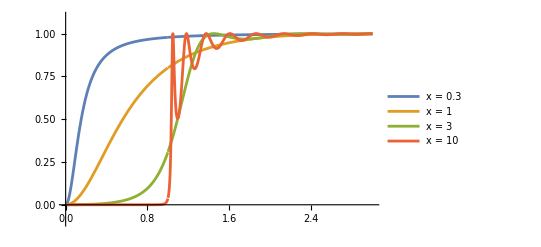

```mathematica
Plot[{Evaluate[(8 ϵ^2 (-1+ϵ^2))/(1-8 ϵ^2+8 ϵ^4-Cos[2 x √(-1+ϵ^2)])/.x->0.3],Evaluate[(8 ϵ^2 (-1+ϵ^2))/(1-8 ϵ^2+8 ϵ^4-Cos[2 x √(-1+ϵ^2)])/.x->1],Evaluate[(8 ϵ^2 (-1+ϵ^2))/(1-8 ϵ^2+8 ϵ^4-Cos[2 x √(-1+ϵ^2)])/.x->3],Evaluate[(8 ϵ^2 (-1+ϵ^2))/(1-8 ϵ^2+8 ϵ^4-Cos[2 x √(-1+ϵ^2)])/.x->10]},{ϵ,0,3},PlotRange->{-0.1,1.1},PlotLegends->{"x = 0.3","x = 1","x = 3","x = 10"}]
```

```mathematica
Limit[(8 ϵ^2 (-1+ϵ^2))/(1-8 ϵ^2+8 ϵ^4-Cos[2 x √(-1+ϵ^2)]),x->∞]//FullSimplify
```

ConditionalExpression[Interval[{1-1/((1-2 ϵ^2)^2),1}], √(-1+ϵ^2)>0]

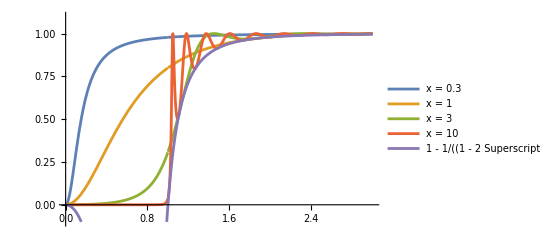

```mathematica
Plot[{Evaluate[(8 ϵ^2 (-1+ϵ^2))/(1-8 ϵ^2+8 ϵ^4-Cos[2 x √(-1+ϵ^2)])/.x->0.3],Evaluate[(8 ϵ^2 (-1+ϵ^2))/(1-8 ϵ^2+8 ϵ^4-Cos[2 x √(-1+ϵ^2)])/.x->1],Evaluate[(8 ϵ^2 (-1+ϵ^2))/(1-8 ϵ^2+8 ϵ^4-Cos[2 x √(-1+ϵ^2)])/.x->3],Evaluate[(8 ϵ^2 (-1+ϵ^2))/(1-8 ϵ^2+8 ϵ^4-Cos[2 x √(-1+ϵ^2)])/.x->10],1-1/((1-2 ϵ^2)^2)},{ϵ,0,3},PlotRange->{-0.1,1.1},PlotLegends->{"x = 0.3","x = 1","x = 3","x = 10","1 - 1/(1 - 2 SuperscriptBox[ϵ, 2])^2"}]
```

## New stuff

```mathematica
Solve[qr^2(u0^2-u^2)+qr(2u u0 ql - 2 u0^2 ql)+1(u^2 ql^2+u0^2 ql^2-2u0 u ql^2+ω0^2)==0,qr]//FullSimplify
```

{{qr→(ql (u-u0) u0-√((u-u0) (ql^2 u^2 (u-u0)+(u+u0) ω0^2)))/(u^2-u0^2)},{qr→(ql (u-u0) u0+√((u-u0) (ql^2 u^2 (u-u0)+(u+u0) ω0^2)))/(u^2-u0^2)}}

```mathematica
H=({{-ω0, ωp/(√2)ⅇ^(ⅈ ϕ), 0}, {ωp/(√2)μ ⅇ^(-ⅈ ϕ), 0, ωp/(√2)μ ⅇ^(ⅈ ϕ)}, {0, ωp/(√2)ⅇ^(-ⅈ ϕ), ω0}});
```

```mathematica
Eigenvalues[H]
```

{0,-√(ω0^2+μ ωp^2),√(ω0^2+μ ωp^2)}

```mathematica
Eigenvectors[H]//FullSimplify
```

{{-ⅇ^(2 ⅈ ϕ),-(√2 ⅇ^(ⅈ ϕ) ω0)/ωp,1},{(ⅇ^(2 ⅈ ϕ) (μ ωp^2+2 ω0 (ω0+√(ω0^2+μ ωp^2))))/(μ ωp^2),-(√2 ⅇ^(ⅈ ϕ) (ω0+√(ω0^2+μ ωp^2)))/ωp,1},{(ⅇ^(2 ⅈ ϕ) (μ ωp^2+2 ω0 (ω0-√(ω0^2+μ ωp^2))))/(μ ωp^2),(√2 ⅇ^(ⅈ ϕ) (-ω0+√(ω0^2+μ ωp^2)))/ωp,1}}

```mathematica
{(ⅇ^(2 ⅈ ϕ) (μ ωp^2+2 ω0 (ω0-√(ω0^2+μ ωp^2))))/(μ ωp^2),(√2 ⅇ^(ⅈ ϕ) (-ω0+√(ω0^2+μ ωp^2)))/ωp,1}*ⅇ^(-ⅈ ϕ)(√(ω0^2+μ ωp^2)+ω0)//FullSimplify
```

{ⅇ^(ⅈ ϕ) (-ω0+√(ω0^2+μ ωp^2)),√2 μ ωp,ⅇ^(-ⅈ ϕ) (ω0+√(ω0^2+μ ωp^2))}

```mathematica
Norm[{(-ω0+√(ω0^2+μ ωp^2)),√2 μ ωp, (ω0+√(ω0^2+μ ωp^2))}]//ComplexExpand//PowerExpand//FullSimplify
```

√(4 ω0^2+2 μ (1+μ) ωp^2)

```mathematica
(4 ω0^2+2 μ (1+μ) ωp^2)/2//Expand
```

2 ω0^2+μ ωp^2+μ^2 ωp^2

```mathematica
{ⅇ^(ⅈ ϕ) (-ω0+√(ω0^2+μ ωp^2)),√2 μ ωp,ⅇ^(-ⅈ ϕ) (ω0+√(ω0^2+μ ωp^2))}/√(4 ω0^2+2 μ (1+μ) ωp^2)/.ϕ->0//FullSimplify
```

{(-ω0+√(ω0^2+μ ωp^2))/(√(4 ω0^2+2 μ (1+μ) ωp^2)),(μ ωp)/(√(2 ω0^2+μ (1+μ) ωp^2)),(ω0+√(ω0^2+μ ωp^2))/(√(4 ω0^2+2 μ (1+μ) ωp^2))}

```mathematica
Norm[{(-ω0+√(ω0^2+μ ωp^2))/(√(4 ω0^2+2 μ (1+μ) ωp^2)),(μ ωp)/(√(2 ω0^2+μ (1+μ) ωp^2)),(ω0+√(ω0^2+μ ωp^2))/(√(4 ω0^2+2 μ (1+μ) ωp^2))}]//ComplexExpand//PowerExpand//FullSimplify
```

1

```mathematica
ψ[ω0_]:=1/(√(2 ω0^2+μ ωp^2+μ^2 ωp^2))({{√2(√(ω0^2+μ ωp^2)-ω0)}, {2μ ωp}, {√2(√(ω0^2+μ ωp^2)+ω0)}})//ComplexExpand//PowerExpand
```

```mathematica
q[ω0_]:=(√(ω^2-ω0^2))/u//ComplexExpand//PowerExpand
```

```mathematica
lhs[x_]:=a ψ[ω0]  ⅇ^(ⅈ q[ω0]x)+b ψ[ω0] ⅇ^(-ⅈ q[ω0]x)/.ω0->0
```

## Scattering with bias

```mathematica
Clear["Global`*"]
```

```mathematica
Solve[u ql - u0 ql ==√((u qr)^2+ω0^2)-u0 qr,qr]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{qr→(ql (u-u0) u0-√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2)},{qr→(ql (u-u0) u0+√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2)}}

```mathematica
(*Take positive qr*)
```

```mathematica
qr=(ql (u-u0) u0+√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2);
```

```mathematica
T=(4 ql qr)/(ql+qr)^2;
```

```mathematica
R=((ql-qr)/(ql+qr))^2;
```

```mathematica
ql=ω/u;ω=α;ω0=1;u=1;u0=γ;
```

```mathematica
Manipulate[Plot[{R/.γ->g,T/.γ->g},{α,0,3},PlotRange->{{0,3},{-0.1,1.1}}],{{g,0},-1,1}]
```

```mathematica
Range[0.4,0.8,0.4]
```

{0.4,0.8}

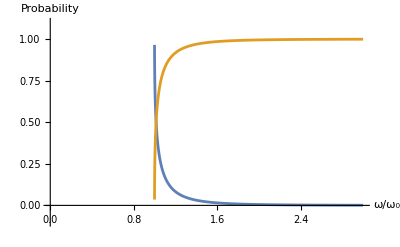

```mathematica
Plot[{R/.γ->0,T/.γ->0},{α,0,3},PlotRange->{{0,3},{-0.1,1.1}},AxesLabel->{"ω/ω_0","Probability"}]
```

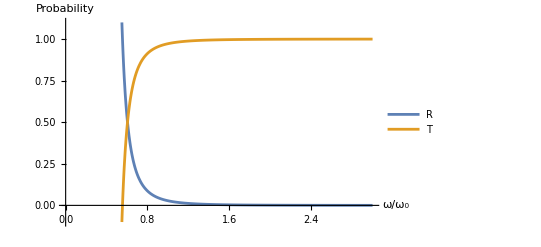
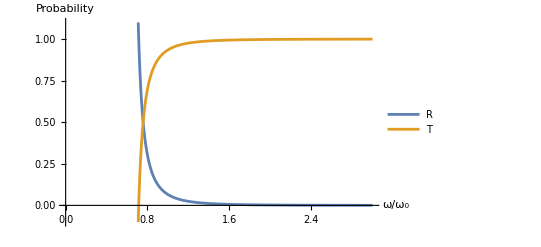
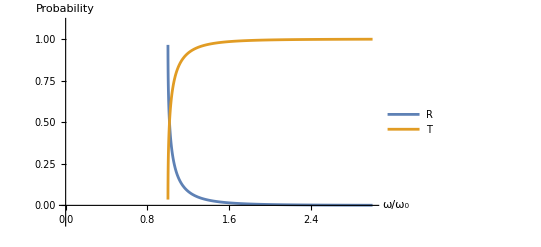
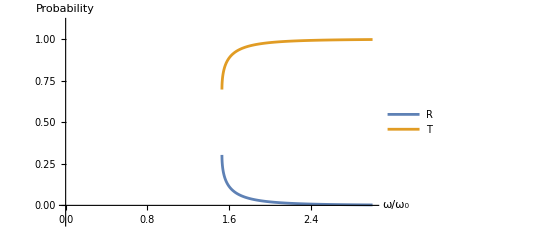
γ = -0.8
-Graphics- | γ = -0.4
-Graphics-
γ = 0.
-Graphics- | γ = 0.4
-Graphics-

```mathematica
attempt1=Partition[Table[{"γ = "<>ToString[g],Plot[{R/.γ->g,T/.γ->g},{α,0,3},PlotRange->{{0,3},{-0.1,1.1}},PlotLegends->{"R","T"},AxesLabel->{"ω/ω_0","Probability"}]},{g,Join[Range[-0.8,0.2,0.4],Range[0.4,0.8,0.4]]}],2]//TableForm
```

```mathematica
Export["attempt1plt.pdf",attempt1]
```

attempt1plt.pdf

```mathematica
(*Checking T + R = 1*)
```

```mathematica
(4 ql u^2 (-1+γ^2) (ql u^2 (-1+γ) γ-√(ql^2 u^4 (-1+γ)^2+u^2 (-1+γ^2) ω0^2)))/((ql u^2 (1+γ-2 γ^2)+√(ql^2 u^4 (-1+γ)^2+u^2 (-1+γ^2) ω0^2))^2)+((ql u^2 (-1+γ)+√(ql^2 u^4 (-1+γ)^2+u^2 (-1+γ^2) ω0^2))^2)/((ql u^2 (1+γ-2 γ^2)+√(ql^2 u^4 (-1+γ)^2+u^2 (-1+γ^2) ω0^2))^2)//FullSimplify//ComplexExpand//PowerExpand
```

1

```mathematica
Manipulate[Plot[{(4 ql u^2 (-1+γ^2) (ql u^2 (-1+γ) γ-√(ql^2 u^4 (-1+γ)^2+u^2 (-1+γ^2) ω0^2)))/((ql u^2 (1+γ-2 γ^2)+√(ql^2 u^4 (-1+γ)^2+u^2 (-1+γ^2) ω0^2))^2),((ql u^2 (-1+γ)+√(ql^2 u^4 (-1+γ)^2+u^2 (-1+γ^2) ω0^2))^2)/((ql u^2 (1+γ-2 γ^2)+√(ql^2 u^4 (-1+γ)^2+u^2 (-1+γ^2) ω0^2))^2)},{γ,-3,3},PlotRange->{{-3,3},{-0.1,1.1}},PlotLegends->{"T","R"},AxesLabel->{"u_0/u","Probability"}],{ql,1,10},{ω0,1,10},{u,1,10}]
```

```mathematica
(*Let (ql u)/ω0 = α, u0/u = γ.*)
```

```mathematica
Evaluate[T/.u0->u γ]/.ql->(α ω0)/u//FullSimplify//PowerExpand//FullSimplify
```

(4 α (-1+γ^2) (α (-1+γ) γ-√(-1+γ) √(1+α^2 (-1+γ)+γ)))/((√(-1+γ) √(1+α^2 (-1+γ)+γ)+α (1+γ-2 γ^2))^2)

```mathematica
Manipulate[Plot[(4 α (-1+γ^2) (α (-1+γ) γ-√(-1+γ) √(1+α^2 (-1+γ)+γ)))/((√(-1+γ) √(1+α^2 (-1+γ)+γ)+α (1+γ-2 γ^2))^2),{α,0,3}],{γ,-1,1}]
```

## Scattering with bias math done properly

```mathematica
Clear["Global`*"]
```

```mathematica
Solve[u ql - u0 ql ==√((u qr)^2+ω0^2)-u0 qr,qr]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{qr→(ql (u-u0) u0-√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2)},{qr→(ql (u-u0) u0+√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2)}}

```mathematica
(*Take positive qr*)
```

```mathematica
qr=(ql (u-u0) u0+√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2);
```

```mathematica
T=(4 ql qr)/(ql+qr)^2;
```

```mathematica
R=((ql-qr)/(ql+qr))^2;
```

```mathematica
(*Let  (ql u)/ω0 = α, u0/u = γ. Both are dimensionless properties*)
```

```mathematica
TProb=Evaluate[T/.u0->u γ]/.ql->(α ω0)/u//FullSimplify//PowerExpand//FullSimplify
```

(4 α (-1+γ^2) (α (-1+γ) γ-√(-1+γ) √(1+α^2 (-1+γ)+γ)))/((√(-1+γ) √(1+α^2 (-1+γ)+γ)+α (1+γ-2 γ^2))^2)

```mathematica
RProb=Evaluate[R/.u0->u γ]/.ql->(α ω0)/u//FullSimplify//PowerExpand//FullSimplify
```

((α (-1+γ)+√(-1+γ) √(1+α^2 (-1+γ)+γ))^2)/((√(-1+γ) √(1+α^2 (-1+γ)+γ)+α (1+γ-2 γ^2))^2)

```mathematica
(*Testing that T+R = 1*)
```

```mathematica
TProb+RProb//FullSimplify
```

1

```mathematica
(*Plotting*)
```

```mathematica
Manipulate[Plot[TProb/.α->a,{γ,-3,3},PlotRange->{{-3,3},{-0.1,1.1}},AxesLabel->{"u_0/u","Probability"}],{a,-3,3}]
```

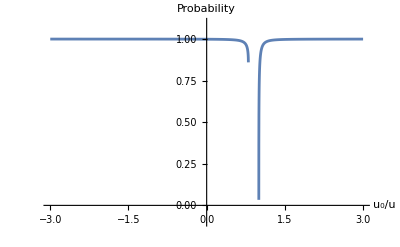
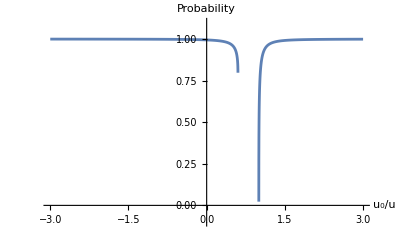
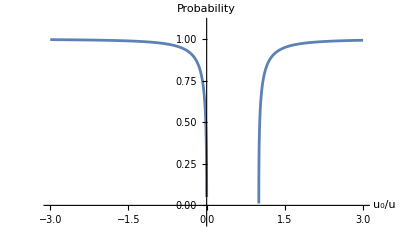
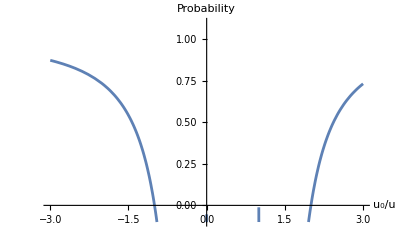
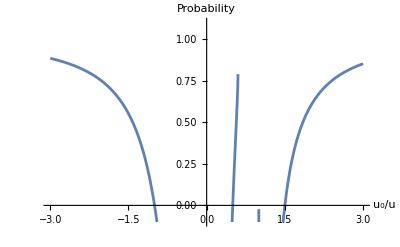
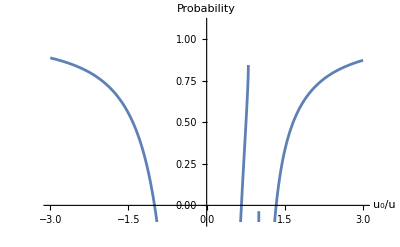
α = -3
-Graphics- | α = -2
-Graphics- | α = -1
-Graphics-
α = 1
-Graphics- | α = 2
-Graphics- | α = 3
-Graphics-

```mathematica
Partition[Table[{"α = "<>ToString[a],Plot[TProb/.α->a,{γ,-3,3},PlotRange->{{-3,3},{-0.1,1.1}},AxesLabel->{"u_0/u","Probability"}]},{a,Join[Range[-3,-1],Range[1,3]]}],3]//TableForm
```

## Scattering properly maybe

```mathematica
Solve[1==((ω-Ω)/(ω+Ω))^2+4X (Ω/(ω+Ω))^2,X]
```

{{X→ω/Ω}}

```mathematica
Solve[a+b==c ωp/Ω&&a-b==c,{b,c}]
```

{{b→-(a (Ω-ωp))/(Ω+ωp),c→(2 a Ω)/(Ω+ωp)}}

```mathematica
Clear["Global`*"]
```

```mathematica
T=(4ωp Ω)/(ωp+Ω)^2;R=((ωp-Ω)/(ωp+Ω))^2;
```

```mathematica
ωp=u qr;Ω = √(ωp^2+ω0^2);
```

```mathematica
Solve[u ql - u0 ql ==√((u qr)^2+ω0^2)-u0 qr,qr]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{qr→(ql (u-u0) u0-√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2)},{qr→(ql (u-u0) u0+√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2)}}

```mathematica
qr=(ql (u-u0) u0-√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2);
```

```mathematica
qr/.u0->0
```

-(√(u (u ω^2-u ω0^2)))/u^2

```mathematica
ωp/.u0->0
```

(√(u (u ω^2-u ω0^2)))/u

```mathematica
Ω/.u0->0//FullSimplify
```

√(ω^2)

```mathematica
ql=ω/u;
```

```mathematica
Variables[T]
```

{u,u0,ω,ω0}

```mathematica
(*Let α = ω/ω0, γ = u0/u*)
```

```mathematica
Evaluate[T/.ω->α ω0]/.u0->u γ//FullSimplify//PowerExpand//FullSimplify
```

(4 √u (α (-1+γ) γ+√(-1+γ) √(1+α^2 (-1+γ)+γ)) √ω0 √(u (γ^2 (1+γ)+2 α √(-1+γ) γ √(1+α^2 (-1+γ)+γ)+α^2 (-1+γ) (1+γ^2)) ω0))/(√(-1+γ) (√u (α √(-1+γ) γ+√(1+α^2 (-1+γ)+γ)) √ω0+√(u (γ^2 (1+γ)+2 α √(-1+γ) γ √(1+α^2 (-1+γ)+γ)+α^2 (-1+γ) (1+γ^2)) ω0))^2)

```mathematica
Evaluate[R/.ω->α ω0]/.u0->u γ//FullSimplify//PowerExpand//FullSimplify
```

((-√u (α √(-1+γ) γ+√(1+α^2 (-1+γ)+γ)) √ω0+√(u (γ^2 (1+γ)+2 α √(-1+γ) γ √(1+α^2 (-1+γ)+γ)+α^2 (-1+γ) (1+γ^2)) ω0))^2)/((√u (α √(-1+γ) γ+√(1+α^2 (-1+γ)+γ)) √ω0+√(u (γ^2 (1+γ)+2 α √(-1+γ) γ √(1+α^2 (-1+γ)+γ)+α^2 (-1+γ) (1+γ^2)) ω0))^2)

```mathematica
Tprob[γ_,α_]:=(4  (1+γ) (α (-1+γ) γ-√(-1+γ) √(1+α^2 (-1+γ)+γ)) √(1+((α (-1+γ) γ-√(-1+γ) √(1+α^2 (-1+γ)+γ))^2)/((-1+γ^2)^2)))/(( (α √(-1+γ) γ-√(1+α^2 (-1+γ)+γ)) +√(γ^2 (1+γ)-2 α √(-1+γ) γ √(1+α^2 (-1+γ)+γ)+α^2 (-1+γ) (1+γ^2)))^2)
```

```mathematica
Rprob[γ_,α_]:=(( (-α √(-1+γ) γ+√(1+α^2 (-1+γ)+γ)) +√(γ^2 (1+γ)-2 α √(-1+γ) γ √(1+α^2 (-1+γ)+γ)+α^2 (-1+γ) (1+γ^2)))^2)/(( (α √(-1+γ) γ-√(1+α^2 (-1+γ)+γ)) +√(γ^2 (1+γ)-2 α √(-1+γ) γ √(1+α^2 (-1+γ)+γ)+α^2 (-1+γ) (1+γ^2)))^2)
```

```mathematica
newTprob[γ_,α_]:=(4 (α (-1+γ) γ+√(-1+γ) √(1+α^2 (-1+γ)+γ))  √(γ^2 (1+γ)+2 α √(-1+γ) γ √(1+α^2 (-1+γ)+γ)+α^2 (-1+γ) (1+γ^2)))/(√(-1+γ) ( (α √(-1+γ) γ+√(1+α^2 (-1+γ)+γ)) +√(γ^2 (1+γ)+2 α √(-1+γ) γ √(1+α^2 (-1+γ)+γ)+α^2 (-1+γ) (1+γ^2)))^2)
```

```mathematica
newRprob[γ_,α_]:=((- (α √(-1+γ) γ+√(1+α^2 (-1+γ)+γ)) +√(γ^2 (1+γ)+2 α √(-1+γ) γ √(1+α^2 (-1+γ)+γ)+α^2 (-1+γ) (1+γ^2)))^2)/(((α √(-1+γ) γ+√(1+α^2 (-1+γ)+γ)) +√(γ^2 (1+γ)+2 α √(-1+γ) γ √(1+α^2 (-1+γ)+γ)+α^2 (-1+γ) (1+γ^2)))^2)
```

```mathematica
Tprob[γ,α]+Rprob[γ,α]//FullSimplify
```

(4 (1+γ) (α (-1+γ) γ-√(-1+γ) √(1+α^2 (-1+γ)+γ)) √(1+((α (-1+γ) γ-√(-1+γ) √(1+α^2 (-1+γ)+γ))^2)/((-1+γ^2)^2))+(-α √(-1+γ) γ+√(1+α^2 (-1+γ)+γ)+√(γ^2 (1+γ)-2 α √(-1+γ) γ √(1+α^2 (-1+γ)+γ)+α^2 (-1+γ) (1+γ^2)))^2)/(α √(-1+γ) γ-√(1+α^2 (-1+γ)+γ)+√(γ^2 (1+γ)-2 α √(-1+γ) γ √(1+α^2 (-1+γ)+γ)+α^2 (-1+γ) (1+γ^2)))^2

```mathematica
Tprob[0,α]//FullSimplify
```

-(4 ⅈ √(α^2-α^4))/((√(-α^2)-√(1-α^2))^2)

```mathematica
-(4 √(α^4-α^2))/((α-√(1-α^2))^2)
```

```mathematica
Tprob[0,0]
```

0

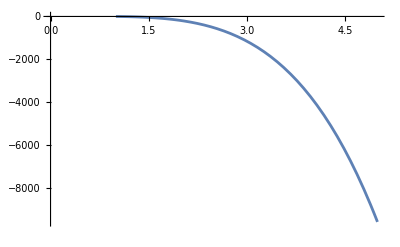

```mathematica
Plot[-(4 ⅈ √(α^2-α^4))/((√(-α^2)-√(1-α^2))^2),{α,0,5}]
```

```mathematica
Manipulate[Plot[{Tprob[γ,α],Rprob[γ,α]},{α,0,3},PlotRange->{{0,3},{-0.1,1.1}},PlotLegends->{"T","R"},AxesLabel->{"ω/ω0", "Probability"}],{γ,-1,1}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Manipulate[Plot[{newTprob[γ,α],newRprob[γ,α]},{α,0,3},PlotRange->{{0,3},{-0.1,1.1}},PlotLegends->{"T","R"},AxesLabel->{"ω/ω0", "Probability"}],{γ,0,1}]
```

```mathematica
Manipulate[Plot[{Tprob[γ,α],Rprob[γ,α],newTprob[γ,α],newRprob[γ,α]},{α,0,3},PlotRange->{{0,3},{-0.1,1.1}},PlotLegends->{"T+","R+","T-","R-"},AxesLabel->{"ω/ω0", "Probability"}],{γ,-1,1}]
```

## Current stuff

```mathematica
Solve[{a+b==c/ν,a-b==c},{b,c}]
```

{{b→-(a (-1+ν))/(1+ν),c→(2 a ν)/(1+ν)}}

```mathematica
1-((ν-1)/(ν+1))^2//Together
```

(4 ν)/(1+ν)^2

```mathematica
(1-γr)/(1-γl)//Apart
```

-1/(-1+γl)+γr/(-1+γl)

```mathematica
Solve[ν ((1-γl)/(1-γr))==1,γl]
```

{{γl→(-1+γr+ν)/ν}}

```mathematica
Clear["Global`*"]
```

```mathematica
1-((ω-Ω)/(ω+Ω))^2//Together
```

(4 ω Ω)/(ω+Ω)^2

## Fixing scattering potential with bias current with frequencies

```mathematica
Clear["Global`*"]
```

```mathematica
T=(4ωp Ω)/(ωp+Ω)^2;R=((ωp-Ω)/(ωp+Ω))^2;Ω = √(ωp^2+ω0^2);
```

```mathematica
Solve[u ql - u0 ql ==√((u qr)^2+ω0^2)-u0 qr,qr]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{qr→(ql (u-u0) u0-√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2)},{qr→(ql (u-u0) u0+√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2)}}

```mathematica
qrp = (ql (u-u0) u0+√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2);qrn = (ql (u-u0) u0-√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2);
```

```mathematica
ωp = u qr;ql=ω/(u-u0);(*CHANGED THIS FROM LAST TIME, USED TO BE ωp = u qr, ω = u ql*)
```

```mathematica
ω=α;ω0=1;u=1;u0=γ;
```

```mathematica
(Tp=T/.qr->qrp);
(Tn=T/.qr->qrn);
(Rp=R/.qr->qrp);
(Rn=R/.qr->qrn);
```

```mathematica
(*Let α = ω/ω0, γ = u0/u*)
```

```mathematica
Tp/.ω->α ω0/.u0->γ u//FullSimplify//PowerExpand//FullSimplify
```

(4 √u (α γ+√(-1+α^2+γ^2)) √ω0 √(u (2 γ (1+γ)+α (α+α γ^2+2 γ √(-1+α^2+γ^2))) ω0))/((√u (α γ+√(-1+α^2+γ^2)) √ω0+√(u (2 γ (1+γ)+α (α+α γ^2+2 γ √(-1+α^2+γ^2))) ω0))^2)

```mathematica
Tpprob[γ_,α_]:=(4 (α γ+√(-1+α^2+γ^2))  √(2 γ (1+γ)+α (α+α γ^2+2 γ √(-1+α^2+γ^2))))/(( (α γ+√(-1+α^2+γ^2)) +√(2 γ (1+γ)+α (α+α γ^2+2 γ √(-1+α^2+γ^2))))^2)
```

```mathematica
Tn/.ω->α ω0/.u0->γ u//FullSimplify//PowerExpand//FullSimplify
```

(4 √u (α γ-√(-1+α^2+γ^2)) √ω0 √(u (2 γ (1+γ)+α (α+α γ^2-2 γ √(-1+α^2+γ^2))) ω0))/((√u (α γ-√(-1+α^2+γ^2)) √ω0+√(u (2 γ (1+γ)+α (α+α γ^2-2 γ √(-1+α^2+γ^2))) ω0))^2)

```mathematica
Tnprob[γ_,α_]:=(4  (α γ-√(-1+α^2+γ^2))  √(2 γ (1+γ)+α (α+α γ^2-2 γ √(-1+α^2+γ^2))))/(((α γ-√(-1+α^2+γ^2)) +√(2 γ (1+γ)+α (α+α γ^2-2 γ √(-1+α^2+γ^2))))^2)
```

```mathematica
Rp/.ω->α ω0/.u0->γ u//FullSimplify//PowerExpand//FullSimplify
```

((-√u (α γ+√(-1+α^2+γ^2)) √ω0+√(u (2 γ (1+γ)+α (α+α γ^2+2 γ √(-1+α^2+γ^2))) ω0))^2)/((√u (α γ+√(-1+α^2+γ^2)) √ω0+√(u (2 γ (1+γ)+α (α+α γ^2+2 γ √(-1+α^2+γ^2))) ω0))^2)

```mathematica
Rpprob[γ_,α_]:=((-(α γ+√(-1+α^2+γ^2)) +√(2 γ (1+γ)+α (α+α γ^2+2 γ √(-1+α^2+γ^2))))^2)/(( (α γ+√(-1+α^2+γ^2)) +√(2 γ (1+γ)+α (α+α γ^2+2 γ √(-1+α^2+γ^2))))^2)
```

```mathematica
Rn/.ω->α ω0/.u0->γ u//FullSimplify//PowerExpand//FullSimplify
```

((√u (-α γ+√(-1+α^2+γ^2)) √ω0+√(u (2 γ (1+γ)+α (α+α γ^2-2 γ √(-1+α^2+γ^2))) ω0))^2)/((√u (α γ-√(-1+α^2+γ^2)) √ω0+√(u (2 γ (1+γ)+α (α+α γ^2-2 γ √(-1+α^2+γ^2))) ω0))^2)

```mathematica
Rnprob[γ_,α_]:=(( (-α γ+√(-1+α^2+γ^2)) +√(2 γ (1+γ)+α (α+α γ^2-2 γ √(-1+α^2+γ^2))))^2)/(((α γ-√(-1+α^2+γ^2)) +√(2 γ (1+γ)+α (α+α γ^2-2 γ √(-1+α^2+γ^2))))^2)
```

```mathematica
γ=0.4
```

0.4

```mathematica
Clear[γ]
```

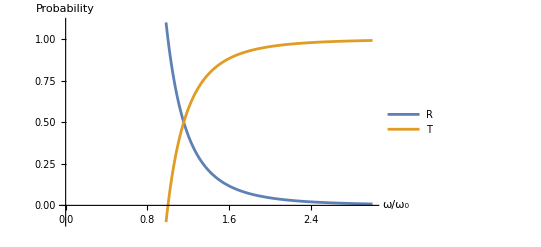
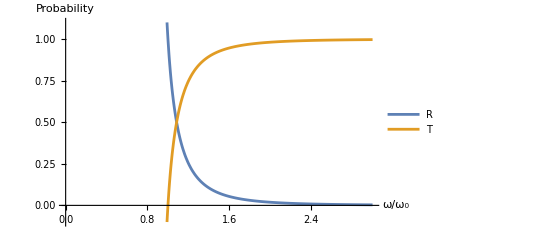
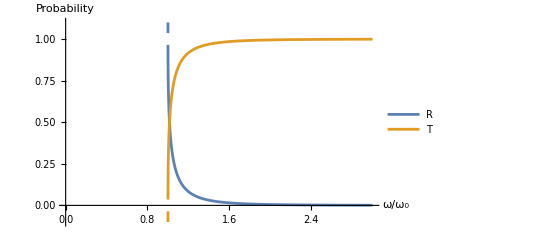
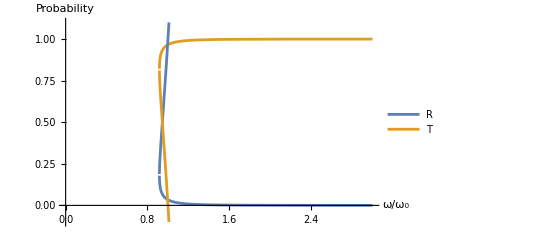
γ = -0.8
-Graphics- | γ = -0.4
-Graphics-
γ = 0.
-Graphics- | γ = 0.4
-Graphics-

```mathematica
attempt2=Partition[Table[{"γ = "<>ToString[g],Plot[{Rp/.γ->g,Tp/.γ->g,Rn/.γ->g,Tn/.γ->g},{α,0,3},PlotRange->{{0,3},{-0.1,1.1}},PlotLegends->{"R","T"},AxesLabel->{"ω/ω_0","Probability"},PlotStyle->{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]]}]},{g,Join[Range[-0.8,0.2,0.4],Range[0.4,0.8,0.4]]}],2]//TableForm
```

```mathematica
Plot[{Tp,Rp,Tn,Rn},{α,0,3},PlotRange->{{0,3},{-0.1,1.1}},PlotLegends->{"T","R"},AxesLabel->{"ω/ω0", "Probability"},PlotStyle->{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]]}]
```

-Graphics-

```mathematica
Export["attempt2plt.pdf",attempt2]
```

attempt2plt.pdf

```mathematica
Manipulate[Plot[{Tpprob[γ,α],Rpprob[γ,α],Tnprob[γ,α],Rnprob[γ,α]},{α,0,3},PlotRange->{{0,3},{-0.1,1.1}},PlotLegends->{"T","R"},AxesLabel->{"ω/ω0", "Probability"},PlotStyle->{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]]}],{γ,-1,1}]
```

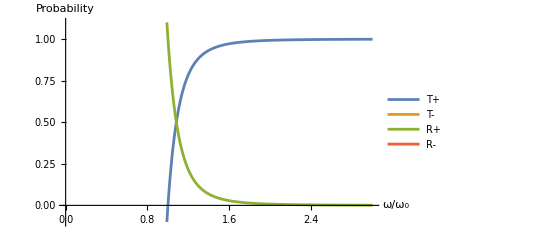
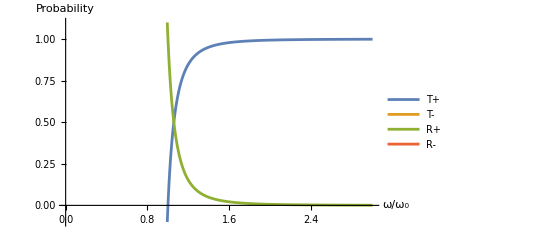
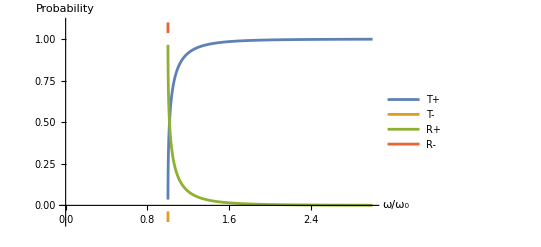
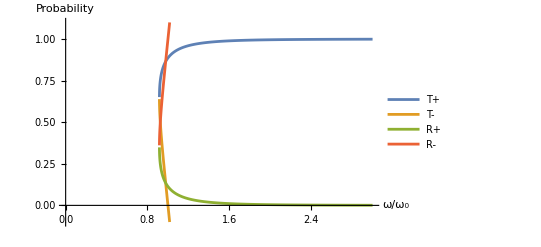
γ = -0.8
-Graphics- | γ = -0.4
-Graphics-
γ = 0.
-Graphics- | γ = 0.4
-Graphics-

```mathematica
Partition[Table[{"γ = "<>ToString[γ],Plot[{Tpprob[γ,α],Tnprob[γ,α],Rpprob[γ,α],Rnprob[γ,α]},{α,0,3},PlotRange->{{0,3},{-0.1,1.1}},PlotLegends->{"T+","T-","R+","R-"},AxesLabel->{"ω/ω_0","Probability"}]},{γ,-0.8,0.4,0.4}],2]//TableForm
```

```mathematica
(*Let u, ω0 = 1*)
```

Ω = √(ωp^2+ω0^2), hence Ω/ω0=√(1+(((u-u0)qr)/ω0)^2) = √(1+((u qr)/ω0(1-γ))^2)=√(1+(ϵ(1-γ))^2).

```mathematica
Manipulate[Plot[{0,√(1+(ϵ(1-γ))^2),-√(1+(ϵ(1-γ))^2)},{ϵ,-3,3},PlotRange->{-5,5}],{γ,-1,1}]
```

```mathematica
Evaluate[qrp/.u0->γ u/.ω->α ω0//FullSimplify//PowerExpand//FullSimplify]*u/ω0//FullSimplify
```

(α γ+√(-1+α^2+γ^2))/(1-γ^2)

```mathematica
Evaluate[qrn/.u0->γ u/.ω->α ω0//FullSimplify//PowerExpand//FullSimplify]*u/ω0//FullSimplify
```

(-α γ+√(-1+α^2+γ^2))/(-1+γ^2)

```mathematica
Evaluate[ql/.u0->γ u/.ω->α ω0//FullSimplify//PowerExpand//FullSimplify]*u/ω0//FullSimplify
```

α/(1-γ)

```mathematica
Manipulate[Plot[{(α γ+√(-1+α^2+γ^2))/(1-γ^2),(-α γ+√(-1+α^2+γ^2))/(-1+γ^2),α/(1-γ)},{α,0,3},PlotRange->{{0,3},{-2,2}},PlotLegends->{"q_R^+ * u/ω0", "q_R^- * u/ω0","ql * u/ω0"},AxesLabel->{"ω/ω0", "q/q"}],{γ,-1,1}]
```

```mathematica
Manipulate[Plot[√((u-u0)^2+1),{u,-3,3},PlotRange->{{-3,3},{-1,5}},AxesLabel->{"u^2/ω_0^2","Ω/ω0"}],{{u0,-3,"u_0^2/ω_0^2"},-3,3}]
```

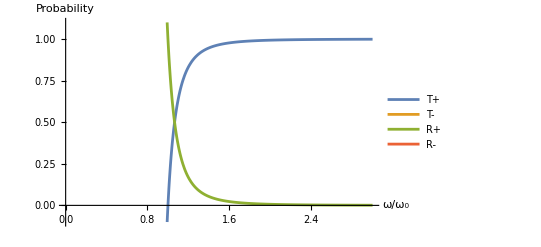
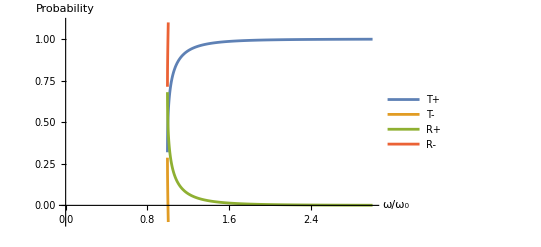
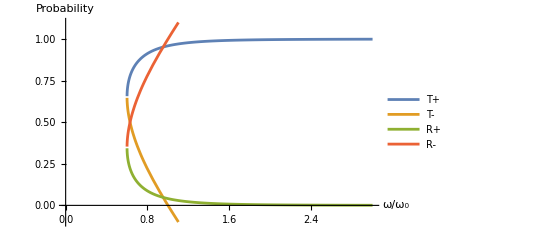
γ = -0.5
-Graphics- | γ = 0.1
-Graphics- | γ = 0.8
-Graphics-

```mathematica
funkyplots=Partition[Table[{"γ = "<>ToString[γ],Plot[{Tpprob[γ,α],Tnprob[γ,α],Rpprob[γ,α],Rnprob[γ,α]},{α,0,3},PlotRange->{{0,3},{-0.1,1.1}},PlotLegends->{"T+","T-","R+","R-"},AxesLabel->{"ω/ω_0","Probability"}]},{γ,{-0.5,0.1, 0.8}}],3]//TableForm
```

```mathematica
Export["plots.pdf",funkyplots]
```

plots.pdf

```mathematica
Manipulate[Plot[{Abs[q]-u0 q, √(q^2+1)-u0 q},{q,-3,3},PlotRange->{{-3,3},{-5,5}}],{u0,-1,1}]
```

```mathematica
D[√(u^2 q^2+ω0^2)-u0 q,q]
```

-u0+(q u^2)/(√(q^2 u^2+ω0^2))

```mathematica
Solve[-u0+(q u^2)/(√(q^2 u^2+ω0^2))==0,q]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{q→-(u0 ω0)/(√(u^4-u^2 u0^2))},{q→(u0 ω0)/(√(u^4-u^2 u0^2))}}

```mathematica
q = (±ωc)/u u0/(√(u^2-u0^2))
```

```mathematica
√((u q)^2+ωc^2)-u0 q/.q->ωc/u u0/(√(u^2-u0^2))//PowerExpand//FullSimplify
```

-(u0^2 ωc)/(u √((u-u0) (u+u0)))+√((u^2 ωc^2)/(u^2-u0^2))

```mathematica
ωm = ωc(√(u^2-u0^2))/u
```

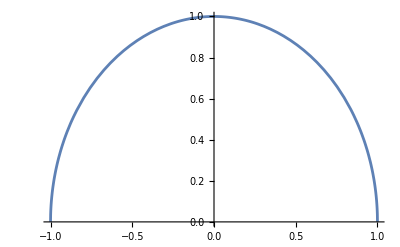

```mathematica
Plot[√(1-γ^2),{γ,-1,1}]
```

```mathematica
Solve[ω==√((u qr)^2+ωc^2)-u0 qr,qr]/.ωc->1/.u->1/.u0->γ
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{qr→(γ ω-√(-1+γ^2+ω^2))/(1-γ^2)},{qr→(γ ω+√(-1+γ^2+ω^2))/(1-γ^2)}}

```mathematica
Solve[ω==u ql - u0 ql, ql]/.ωc->1/.u->1/.u0->γ
```

{{ql→ω/(1-γ)}}

```mathematica
Manipulate[Plot[ω/(1-γ),{ω,0,3},PlotRange->{{0,3},{-6,6}}],{γ,-1,1}]
```

```mathematica
Manipulate[Plot[{Abs[(γ ω+√(-1+γ^2+ω^2))/(1-γ^2)]},{ω,0,3},PlotRange->{{0,3},{-6,6}}],{γ,-1,1}]
```

```mathematica
Manipulate[Plot[{(γ ω+√(-1+γ^2+ω^2))/(1-γ^2)},{ω,0,3},PlotRange->{{0,3},{-6,6}}],{γ,-1,1}]
```

```mathematica
(*qr is positive*)
```

```mathematica
Clear["Global`*"]
```

```mathematica
qr=(γ ω+√(-1+γ^2+ω^2))/(1-γ^2);
```

```mathematica
T=(4ωp Ω)/(ωp+Ω)^2;R=((ωp-Ω)/(ωp+Ω))^2;Ω = √(ωp^2+ω0^2);
```

```mathematica
ωp = u qr;ω0=1;u=1;
```

```mathematica
Manipulate[Plot[qr/.γ->g,{ω,0,3},PlotRange->{{0,3},{-3,3}}],{g,-1,1}]
```

```mathematica
Ω//FullSimplify//PowerExpand//FullSimplify
```

√(1+((γ ω+√(-1+γ^2+ω^2))^2)/((-1+γ^2)^2))

```mathematica
T
```

(4 (γ ω+√(-1+γ^2+ω^2)) √(1+((γ ω+√(-1+γ^2+ω^2))^2)/((1-γ^2)^2)))/((1-γ^2) ((γ ω+√(-1+γ^2+ω^2))/(1-γ^2)+√(1+((γ ω+√(-1+γ^2+ω^2))^2)/((1-γ^2)^2)))^2)

```mathematica
R
```

(((γ ω+√(-1+γ^2+ω^2))/(1-γ^2)-√(1+((γ ω+√(-1+γ^2+ω^2))^2)/((1-γ^2)^2)))^2)/(((γ ω+√(-1+γ^2+ω^2))/(1-γ^2)+√(1+((γ ω+√(-1+γ^2+ω^2))^2)/((1-γ^2)^2)))^2)

```mathematica
Manipulate[Plot[{(4 (γ ω+√(-1+γ^2+ω^2)) √(1+((γ ω+√(-1+γ^2+ω^2))^2)/((1-γ^2)^2)))/((1-γ^2) ((γ ω+√(-1+γ^2+ω^2))/(1-γ^2)+√(1+((γ ω+√(-1+γ^2+ω^2))^2)/((1-γ^2)^2)))^2),(((γ ω+√(-1+γ^2+ω^2))/(1-γ^2)-√(1+((γ ω+√(-1+γ^2+ω^2))^2)/((1-γ^2)^2)))^2)/(((γ ω+√(-1+γ^2+ω^2))/(1-γ^2)+√(1+((γ ω+√(-1+γ^2+ω^2))^2)/((1-γ^2)^2)))^2)},{ω,0,3},PlotLegends->{"T","R"},PlotRange->{{0,3},{0,1}}],{γ,-1,1}]
```

```mathematica
wt[g_]:=√(1-g^2);
wp[w_,g_]:=(g w+√(-1+g^2+w^2))/(1-g^2);
Om[w_,g_]:=Sqrt[1+qrn[w,g]^2]
```

```mathematica
Clear[T]
```

```mathematica
T[w_,g_]:=(4wp[w,g]Om[w,g])/(wp[w,g]+Om[w,g])^2
```

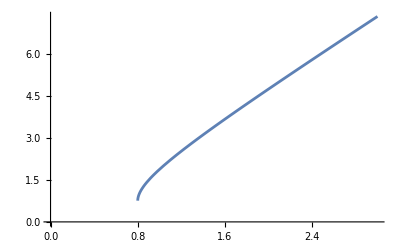

```mathematica
Plot[wp[w,0.6],{w,0,3}]
```

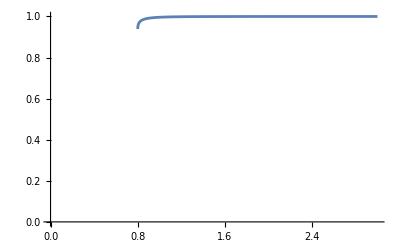

```mathematica
Plot[T[w,0.6],{w,0,3},PlotRange->{{0,3},{0,1}}]
```

```mathematica
T[0.5,0.6]
```

1.05652-0.0266815 ⅈ

```mathematica
wt[0.8]
```

0.6

Solve same way as before when Qr is positive, flip spinor when Qr is negative

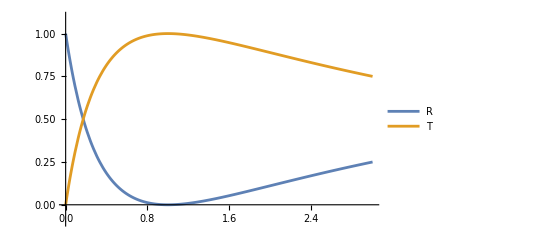

```mathematica
Plot[{((ν-1)/(ν+1))^2,(4ν)/(ν+1)^2},{ν,0,3},PlotRange->{{0,3},{-0.1,1.1}},PlotLegends->{"R","T"}]
```

## More new stuff

```mathematica
Clear["Global`*"]
```

```mathematica
Solve[{1-b==-c,1+b==ωp/Ω c},{b,c}]//FullSimplify
```

{{b→1+(2 Ω)/(-Ω+ωp),c→(2 Ω)/(-Ω+ωp)}}

```mathematica
Solve[Abs[1+(2 Ω)/(-Ω+ωp)]^2+x Abs[(2 Ω)/(-Ω+ωp)]^2==1,x]//FullSimplify
```

{{x→-(ωp Conjugate[Ω]+Ω Conjugate[ωp])/(2 Abs[Ω]^2)}}

```mathematica
Solve[((ωp-Ω)/(ωp+Ω))^2+x((2Ω)/(ωp+Ω))^2==1,x]
```

{{x→ωp/Ω}}

```mathematica
Solve[{a-b==c,a+b==μ^2 ωp/Ω c},{b,c}]
```

{{b→-(a (Ω-μ^2 ωp))/(Ω+μ^2 ωp),c→(2 a Ω)/(Ω+μ^2 ωp)}}

```mathematica
Solve[((μ^2 ωp-Ω)/(μ^2 ωp+Ω))^2+x((2Ω)/(Ω+μ^2 ωp))^2==1,x]
```

{{x→(μ^2 ωp)/Ω}}

```mathematica
ψ={ⅇ^(ⅈ ϕ)/2(1-ω0/Ω),1/(√2)μ ωp/Ω,ⅇ^(-ⅈ ϕ)/2(1+ω0/Ω)};
```

```mathematica
Evaluate[ψ.ψ*//ComplexExpand//Together]/.Ω->√(ω0^2+μ ωp^2)
```

(2 ω0^2+μ ωp^2+μ^2 ωp^2)/(2 (ω0^2+μ ωp^2))

```mathematica
√(1/((2 ω0^2+μ ωp^2+μ^2 ωp^2)/(2 (ω0^2+μ ωp^2))))/.ω0->0//FullSimplify
```

√2 √(1/(1+μ))

```mathematica
Solve[{(a+b)√(1/(μ+μ^2))==c √((2 ω0^2+2μ ωp^2)/(2 ω0^2+μ ωp^2+μ^2 ωp^2))*1/(√2)μ ωp/Ω,(a-b)√(2/(1+μ))==c √((2 ω0^2+2μ ωp^2)/(2 ω0^2+μ ωp^2+μ^2 ωp^2))},{b,c}]//PowerExpand//FullSimplify
```

{{b→(a (-√(1+μ) Ω+μ √(μ (1+μ)) ωp))/(√(1+μ) Ω+μ √(μ (1+μ)) ωp),c→(2 a Ω √(2 ω0^2+μ (1+μ) ωp^2))/(√(1+μ) (Ω+μ^(3/2) ωp) √(ω0^2+μ ωp^2))}}

```mathematica
{{b->(a (-√(1+μ) Ω+μ √(μ (1+μ)) ωp))/(√(1+μ) Ω+μ √(μ (1+μ)) ωp),c->(2 a Ω √(2 ω0^2+μ (1+μ) ωp^2))/(√(1+μ) (Ω+μ^(3/2) ωp) √(ω0^2+μ ωp^2))}}/.Ω->√(ω0^2+μ ωp^2)//FullSimplify
```

{{b→(a (μ √(μ (1+μ)) ωp-√(1+μ) √(ω0^2+μ ωp^2)))/(μ √(μ (1+μ)) ωp+√(1+μ) √(ω0^2+μ ωp^2)),c→(2 a √(2 ω0^2+μ (1+μ) ωp^2))/(√(1+μ) (μ^(3/2) ωp+√(ω0^2+μ ωp^2)))}}

```mathematica
(μ √(μ (1+μ)) ωp-√(1+μ) √(ω0^2+μ ωp^2))/(μ √(μ (1+μ)) ωp+√(1+μ) √(ω0^2+μ ωp^2))
```

(μ √(μ (1+μ)) ωp-√(1+μ) √(ω0^2+μ ωp^2))/(μ √(μ (1+μ)) ωp+√(1+μ) √(ω0^2+μ ωp^2))

```mathematica
R=((μ ωp-Ω)/(μ ωp+Ω))^2;1-R//FullSimplify
```

(4 μ Ω ωp)/(Ω+μ ωp)^2

## New spinor experimentation?

```mathematica
Clear["Global`*"]
```

```mathematica
R=(Abs[μ ωp-Ω]/Abs[μ ωp+Ω])^2;T=1-R;Ω=√(ω0^2+μ ωp^2);ωp=(u-u0) qr;ql=ω/(u-u0);
```

```mathematica
(*Let α = ω/ω0, γ = u0/u*)
```

```mathematica
ω=α ω0;u0 = u γ;
```

```mathematica
Solve[u ql - u0 ql ==√((u qr)^2+ω0^2)-u0 qr,qr]//FullSimplify//PowerExpand//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{qr→((α γ+√(-1+α^2+γ^2)) ω0)/(u-u γ^2)},{qr→((-α γ+√(-1+α^2+γ^2)) ω0)/(u (-1+γ^2))}}

```mathematica
qr=((α γ+√(-1+α^2+γ^2)) ω0)/(u-u γ^2);u=1;ω0=1;
```

```mathematica
Manipulate[Plot[{T/.{γ->g,μ->m},R/.{γ->g,μ->m}},{α,0,3},PlotRange->{{0,3},{-0.1,1.1}},PlotLegends->{"T+","T-","R+","R-"},AxesLabel->{"ω/ω_0","Probability"}],{{g,-1,"u_0/u = "},-1,1},{{m,1,"ρ_0/ρ = "},0,1}]
```

## From start

```mathematica
Clear["Global`*"]
```

Dispersion relation

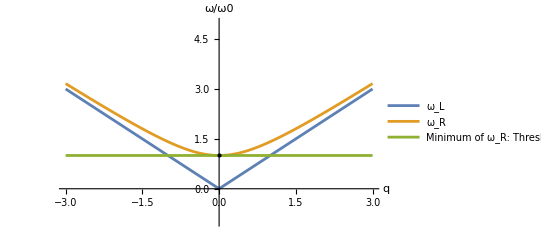

```mathematica
disprel0=With[{u0=0},Plot[{Abs[q]-u0 q, √(q^2+1)-u0 q,√(1-u0^2)},{q,-3,3},PlotRange->{{-3,3},{-1,5}},PlotLegends->{"ω_L", "ω_R","Minimum of ω_R: Threshold"},AxesLabel->{"q","ω/ω0"},Epilog->{Style[Point[{u0/(√(1-u0^2)),√(1-u0^2)}],Green,AbsolutePointSize[10]]}]]
```

```mathematica
Export["disprel0.pdf",disprel0]
```

disprel0.pdf

```mathematica
Export["disprel9.pdf",disprel9]
```

disprel9.pdf

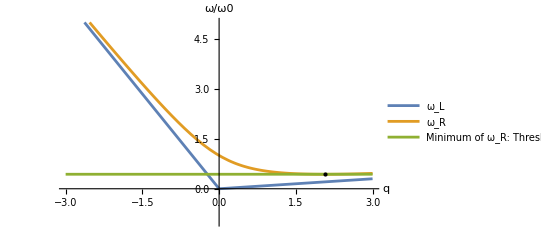

```mathematica
disprel9=With[{u0=0.9},Plot[{Abs[q]-u0 q, √(q^2+1)-u0 q,√(1-u0^2)},{q,-3,3},PlotRange->{{-3,3},{-1,5}},PlotLegends->{"ω_L", "ω_R","Minimum of ω_R: Threshold"},AxesLabel->{"q","ω/ω0"},Epilog->{Style[Point[{u0/(√(1-u0^2)),√(1-u0^2)}],Green,AbsolutePointSize[10]]}]]
```

```mathematica
manplt=Manipulate[Plot[{Abs[q]-u0 q, √(q^2+1)-u0 q,√(1-u0^2)},{q,-3,3},PlotRange->{{-3,3},{-5,5}},PlotLegends->{"ω_L", "ω_R","Minimum of ω_R: Threshold"},AxesLabel->{"q","ω/ω0"},Epilog->{Style[Point[{u0/(√(1-u0^2)),√(1-u0^2)}],Green,AbsolutePointSize[10]]}],{{u0,0.85, "γ = "},-1,1}]
```

```mathematica
Export["manipulate.pdf",manplt]
```

manipulate.pdf

```mathematica
Solve[√(1-u0^2)==0.5,u0]
```

{{γ→-0.866025},{γ→0.866025}}

When γ < 0, q_R is negative.

```mathematica
T=(4ωp Ω)/(ωp+Ω)^2;R=((ωp-Ω)/(ωp+Ω))^2;Ω = √(ωp^2+ω0^2);
```

```mathematica
Solve[u ql - u0 ql ==√((u qr)^2+ω0^2)-u0 qr,qr]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{qr→(ql (u-u0) u0-√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2)},{qr→(ql (u-u0) u0+√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2)}}

```mathematica
Solve[u ql + u0 ql ==√((u qr)^2+ω0^2)+u0 qr,qr]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{qr→-(ql u0 (u+u0)+√((u+u0) (ql^2 u^2 (u+u0)+(-u+u0) ω0^2)))/(u^2-u0^2)},{qr→(-ql u0 (u+u0)+√((u+u0) (ql^2 u^2 (u+u0)+(-u+u0) ω0^2)))/(u^2-u0^2)}}

```mathematica
u=1;ω0=1;
```

```mathematica
qrpp[ql_,u0_]:=(ql (u-u0) u0+√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2);qrpn[ql_,u0_]:=(ql (u-u0) u0-√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2);qrnp[ql_,u0_]:=(-ql u0 (u+u0)+√((u+u0) (ql^2 u^2 (u+u0)+(-u+u0) ω0^2)))/(u^2-u0^2);qrnn[ql_,u0_]:=-(ql u0 (u+u0)+√((u+u0) (ql^2 u^2 (u+u0)+(-u+u0) ω0^2)))/(u^2-u0^2);
```

```mathematica
Manipulate[Plot[{qrpp[ql,u0],qrpn[ql,u0],qrnp[ql,u0],qrnn[ql,u0]},{ql,-3,3},PlotLegends->{"qrpp","qrpn","qrnp","qrnn"},PlotRange->{{-3,3},{-8,8}},AxesLabel->{"ql","qr"}],{u0,-1,1}]
```

```mathematica
Clear["Global`*"]
```

```mathematica
Solve[u ql - u0 ql ==√((u qr)^2+ω0^2)-u0 qr,qr]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{qr→(ql (u-u0) u0-√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2)},{qr→(ql (u-u0) u0+√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2)}}

```mathematica
(*Take positive branch*)
```

```mathematica
qrp=(ql (u-u0) u0+√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2);
```

```mathematica
T=(4ωp Ω)/(ωp+Ω)^2;R=((ωp-Ω)/(ωp+Ω))^2;Ω = √(ωp^2+ω0^2);ωp = (u-u0)qr;ql=ω/(u-u0);
```

```mathematica
Tp = T/.qr->qrp;Tn = T/.qr->qrn;Rp=R/.qr->qrp;Rn=R/.qr->qrn;
```

```mathematica
ω=α ω0;u0 = γ u;
```

```mathematica
u=1;ω0=1;
```

```mathematica
qrn=(ql (u-u0) u0-√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2);
```

```mathematica
Manipulate[Plot[{Tp/.γ->g,Tn/.γ->g,Rp/.γ->g,Rn/.γ->g},{α,0,3},PlotRange->{{0,3},{-0.1,1.1}},PlotLegends->{"T+","T-","R+","R-"},AxesLabel->{"ω/ω0", "Probability"}],{{g,-0.8},-1,1}]
```

## Maybe fixed?

```mathematica
Clear["Global`*"]
```

```mathematica
Solve[(Abs[(ωp-Ω)/(ωp+Ω)])^2+x Abs[(2Ω)/(ωp+Ω)]^2==1,x](*|A|^2 = |B|^2 + x |C|^2, using absolute values as required*)
```

{{x→(1-Abs[(-Ω+ωp)/(Ω+ωp)]^2)/(4 Abs[Ω/(Ω+ωp)]^2)}}

```mathematica
Solve[u ql - u0 ql ==√((u qr)^2+ω0^2)-u0 qr,qr]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{qr→(ql (u-u0) u0-√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2)},{qr→(ql (u-u0) u0+√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2)}}

```mathematica
(*Take positive branch*)
```

```mathematica
qr=(ql (u-u0) u0+√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2);
```

```mathematica
ωp = (u-u0)qr;ql=ω/(u-u0);
```

```mathematica
T=(1-Abs[(-Ω+ωp)/(Ω+ωp)]^2)/(4 Abs[Ω/(Ω+ωp)]^2)Abs[(2Ω)/(ωp+Ω)]^2;R=(Abs[(ωp-Ω)/(ωp+Ω)])^2;Ω = √(ωp^2+ω0^2);
```

```mathematica
ω=α ω0;u0 = γ u;u=1;ω0=1;
```

```mathematica
(*Red dashed line indicates threshold. Note: Threshold does not matter when γ < 0, as this implies ω < 0 branch*)
```

```mathematica
Manipulate[Plot[{R/.γ->g,T/.γ->g},{α,0,3},PlotRange->{{0,3},{-0.1,1.1}},PlotLegends->{"R","T"},AxesLabel->{"ω/ω_0", "Probability"},Epilog->{Red,Dashed,Line[{{√(1-g^2),-0.1},{√(1-g^2),1.1}}]}],{{g,-0.8,"u_0/u = "},-1,1}]
```

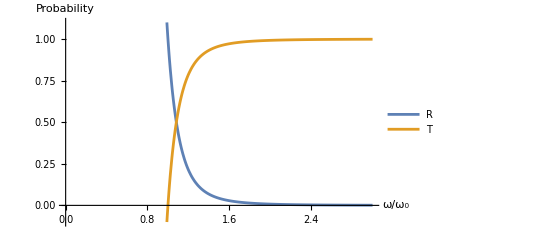
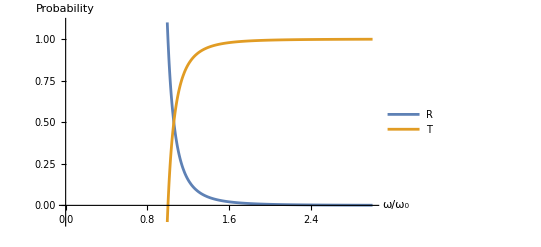
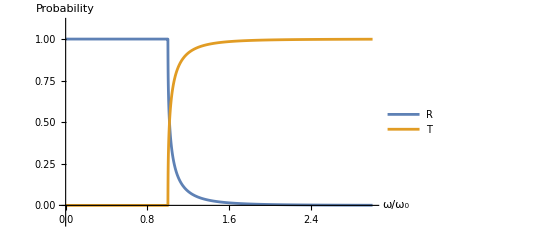
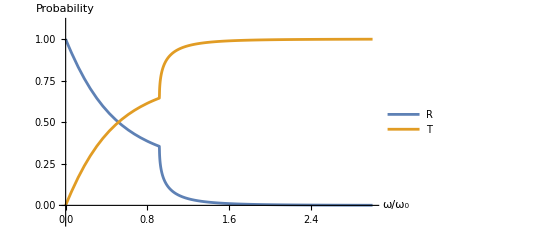
γ = -0.8
-Graphics- | γ = -0.4
-Graphics-
γ = 0.
-Graphics- | γ = 0.4
-Graphics-

```mathematica
attempt3=Partition[Table[{"γ = "<>ToString[g],Plot[{R/.γ->g,T/.γ->g},{α,0,3},PlotRange->{{0,3},{-0.1,1.1}},PlotLegends->{"R","T"},AxesLabel->{"ω/ω_0","Probability"}]},{g,Join[Range[-0.8,0.2,0.4],Range[0.4,0.8,0.4]]}],2]//TableForm
```

```mathematica
Export["attempt3plt.pdf",attempt3]
```

attempt3plt.pdf

## Using matrices?

```mathematica
Clear["Global`*"]
```

```mathematica
(*Finding coefficients A, B and C*)
```

```mathematica
Solve[{(u-u0)a+(-u-u0)b==((u ωp)/Ω-u0)c,a+b==ωp/Ω c},{b,c}]//FullSimplify
```

{{b→(a u0 (-Ω+ωp))/(u0 Ω-(2 u+u0) ωp),c→(2 a u Ω)/(2 u ωp+u0 (-Ω+ωp))}}

```mathematica
(*Finding R and T from A, B and C*)
```

```mathematica
Solve[Abs[(u0 (-Ω+ωp))/(u0 Ω-(2 u+u0) ωp)]^2+x Abs[(2  u Ω)/(2 u ωp+u0 (-Ω+ωp))]^2==1,x]
```

{{x→(1-Abs[(u0 (-Ω+ωp))/(u0 Ω-(2 u+u0) ωp)]^2)/(4 Abs[(u Ω)/(2 u ωp+u0 (-Ω+ωp))]^2)}}

```mathematica
R=Abs[(u0 (-Ω+ωp))/(u0 Ω-(2 u+u0) ωp)]^2;T = (1-Abs[(u0 (-Ω+ωp))/(u0 Ω-(2 u+u0) ωp)]^2)/(4 Abs[(u Ω)/(2 u ωp+u0 (-Ω+ωp))]^2)Abs[(2  u Ω)/(2 u ωp+u0 (-Ω+ωp))]^2;
```

```mathematica
(*Find q_R in terms of u, u0 and q_L*)
```

```mathematica
Solve[u ql - u0 ql ==√((u qr)^2+ω0^2)-u0 qr,qr]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{qr→(ql (u-u0) u0-√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2)},{qr→(ql (u-u0) u0+√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2)}}

```mathematica
qr=(ql (u-u0) u0+√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2);
```

```mathematica
(*Defining variables. q_R = ω_p/u, q_L = ω/(u-u_0), and letting α = ω/ω_0, γ = u_0/u.)
```

```mathematica
ωp =u qr;ql=ω/(u-u0);Ω = √(ωp^2+ω0^2);ω=α ω0;u0 = γ u;
```

```mathematica
u=1;ω0=1;
```

```mathematica
(*Plotting R and T, along with the threshold*)
```

```mathematica
Manipulate[Plot[{R/.γ->g,T/.γ->g},{α,0,3},PlotRange->{{0,3},{-0.1,1.1}},PlotLegends->{"R","T"},AxesLabel->{"ω/ω_0", "Probability"},Epilog->{Red,Dashed,Line[{{√(1-g^2),-0.1},{√(1-g^2),1.1}}]}],{{g,-0.8,"u_0/u = "},-1,1}]
```

## This better be the run

```mathematica
Clear["Global`*"]
```

```mathematica
T = (u ωp/Ω-u0)/(u-u0)Abs[(2u Ω)/(2 u ωp+u0 (ωp-Ω))]^2;R=(u+u0)/(u-u0)Abs[(u0 (ωp-Ω))/(u0 Ω-(2 u+u0) ωp)]^2;
```

```mathematica
Solve[u ql - u0 ql ==√((u qr)^2+ω0^2)-u0 qr,qr]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{qr→(ql (u-u0) u0-√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2)},{qr→(ql (u-u0) u0+√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2)}}

```mathematica
qr=(ql (u-u0) u0+√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2);
```

```mathematica
ωp =u qr;ql=ω/(u-u0);Ω = √(ωp^2+ω0^2);ω=α ω0;u0 = γ u;
```

```mathematica
u=1;ω0=1;
```

```mathematica
Manipulate[Plot[{R/.γ->g,T/.γ->g},{α,0,3},PlotRange->{{0,3},{-0.1,1.1}},PlotLegends->{"R","T"},AxesLabel->{"ω/ω_0", "Probability"},Epilog->{Red,Dashed,Line[{{√(1-g^2),-0.1},{√(1-g^2),1.1}}]}],{{g,-0.8,"u_0/u = "},-1,1}]
```

## This is it?

```mathematica
Clear["Global`*"]
```

```mathematica
Solve[{a-b==c,a+b==ωp/Ω c},{b,c}]
```

{{b→-(a (Ω-ωp))/(Ω+ωp),c→(2 a Ω)/(Ω+ωp)}}

```mathematica
R=(u+u0)/(u-u0)Abs[(ωp-Ω)/(ωp+Ω)]^2;T=(u ωp/Ω-u0)/(u-u0)Abs[(2Ω)/(ωp+Ω)]^2;
```

```mathematica
Solve[u ql - u0 ql ==√((u qr)^2+ω0^2)-u0 qr,qr]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{qr→(ql (u-u0) u0-√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2)},{qr→(ql (u-u0) u0+√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2)}}

```mathematica
qr=(ql (u-u0) u0+√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2);
```

```mathematica
ωp =u qr;ql=ω/(u-u0);Ω = √(ωp^2+ω0^2);ω=α ω0;u0 = γ u;
```

```mathematica
u=1;ω0=1;
```

```mathematica
Manipulate[Plot[{R/.γ->g,T/.γ->g},{α,0,3},PlotRange->{{0,3},{-0.1,3}},PlotLegends->{"R","T"},AxesLabel->{"ω/ω_0", "Probability"},Epilog->{Red,Dashed,Line[{{√(1-g^2),-0.1},{√(1-g^2),4}}],Black,Dashed,Line[{{0,1},{3,1}}]}],{{g,-0.8,"u_0/u = "},-1,1}]
```

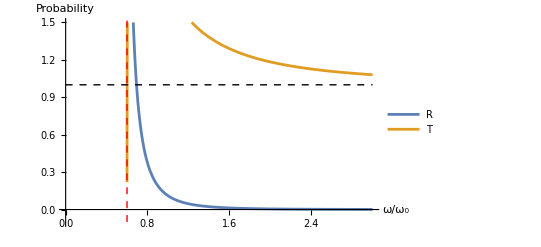
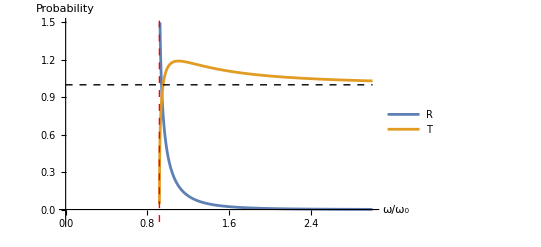
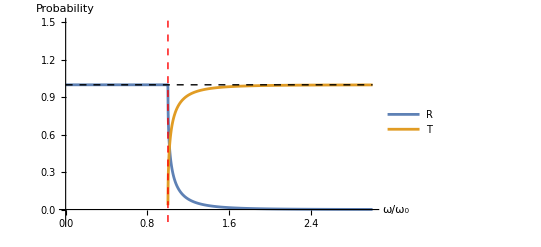
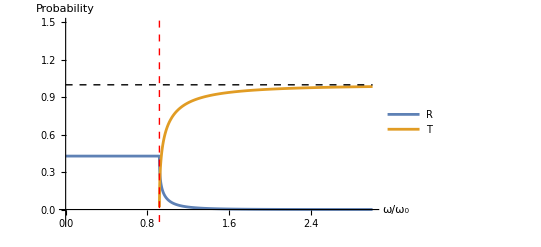
γ = -0.8
-Graphics- | γ = -0.4
-Graphics-
γ = 0.
-Graphics- | γ = 0.4
-Graphics-

```mathematica
attempt4=Partition[Table[{"γ = "<>ToString[g],Plot[{R/.γ->g,T/.γ->g},{α,0,3},PlotRange->{{0,3},{-0.1,1.5}},PlotLegends->{"R","T"},AxesLabel->{"ω/ω_0","Probability"},Epilog->{Red,Dashed,Line[{{√(1-g^2),-0.1},{√(1-g^2),4}}],Black,Dashed,Line[{{0,1},{3,1}}]}]},{g,Join[Range[-0.8,0.2,0.4],Range[0.4,0.8,0.4]]}],2]//TableForm
```

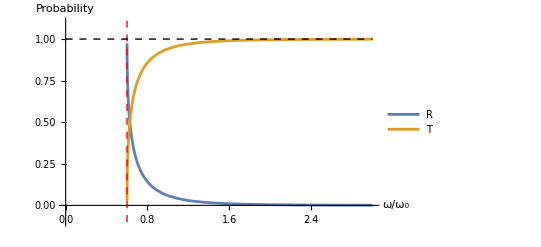
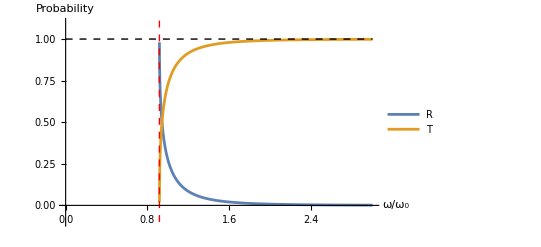
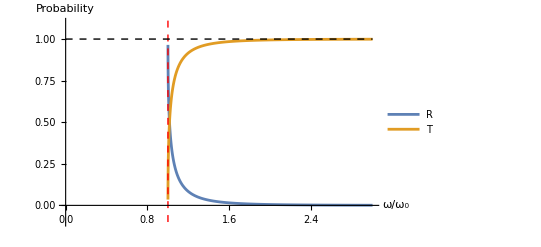
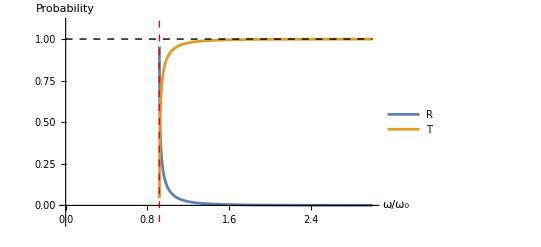
γ = -0.8
-Graphics- | γ = -0.4
-Graphics-
γ = 0.
-Graphics- | γ = 0.4
-Graphics-

```mathematica
normalizednaive=Partition[Table[{"γ = "<>ToString[g],Plot[{R/(R+T)/.γ->g,T/(R+T)/.γ->g},{α,0,3},PlotRange->{{0,3},{-0.1,1.1}},PlotLegends->{"R","T"},AxesLabel->{"ω/ω_0","Probability"},Epilog->{Red,Dashed,Line[{{√(1-g^2),-0.1},{√(1-g^2),4}}],Black,Dashed,Line[{{0,1},{3,1}}]}]},{g,Join[Range[-0.8,0.2,0.4],Range[0.4,0.8,0.4]]}],2]//TableForm
```

```mathematica
Export["normalizednaive.pdf",normalizednaive]
```

normalizednaive.pdf

```mathematica
Export["attempt4plt.pdf",attempt4]
```

attempt4plt.pdf

## Maybe changes

```mathematica
Solve[u Abs[ql] - u0 ql ==√((u qr)^2+ω0^2)-u0 qr,qr]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{qr→-(-ql γ^2+γ Abs[ql]+√(ql^2 γ^2+(-1+γ^2) ω0^2+Abs[ql] (-2 ql γ+Abs[ql])))/(-1+γ^2)},{qr→(ql γ^2-γ Abs[ql]+√(ql^2 γ^2+(-1+γ^2) ω0^2+Abs[ql] (-2 ql γ+Abs[ql])))/(-1+γ^2)}}

```mathematica
Solve[u ql - u0 ql ==√((u qr)^2+ω0^2)-u0 qr,qr]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{qr→(ql (u-u0) u0-√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2)},{qr→(ql (u-u0) u0+√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2)}}

```mathematica
Clear["Global`*"]
```

```mathematica
(*qr=(ql γ^2-γ Abs[ql]+√(ql^2 γ^2+(-1+γ^2) ω0^2+Abs[ql] (-2 ql γ+Abs[ql])))/(-1+γ^2);*)qr=(ql (u-u0) u0+√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2);
```

```mathematica
R=(u+u0)/(u-u0)Abs[(ωp-Ω)/(ωp+Ω)]^2;T=(u ωp/Ω-u0)/(u-u0)Abs[(2Ω)/(ωp+Ω)]^2;ωp =u qr;ql=ω/(u-u0);Ω = √(ωp^2+ω0^2);ω=α ω0;u0 = γ u;u=1;u0=γ;ω0=1;
```

```mathematica
Manipulate[Plot[{R/.γ->g,T/.γ->g},{α,0,3},PlotRange->{{0,3},{-0.1,1.1}},PlotLegends->{"R","T"},AxesLabel->{"ω/ω_0", "Probability"},Epilog->{Red,Dashed,Line[{{√(1-g^2),-0.1},{√(1-g^2),1.1}}],Black,Dashed,Line[{{0,1},{3,1}}]}],{{g,-0.8,"u_0/u = "},-1,1}]
```

```mathematica
ωpn=-(-(α γ^2)/(1-γ)+γ Abs[α/(1-γ)]+√(-1+γ^2+(α^2 γ^2)/(1-γ)^2+Abs[α/(1-γ)] (-(2 α γ)/(1-γ)+Abs[α/(1-γ)])))/(-1+γ^2)
```

-(-(α γ^2)/(1-γ)+γ Abs[α/(1-γ)]+√(-1+γ^2+(α^2 γ^2)/(1-γ)^2+Abs[α/(1-γ)] (-(2 α γ)/(1-γ)+Abs[α/(1-γ)])))/(-1+γ^2)

```mathematica
ωp
```

((α γ^2)/(1-γ)-γ Abs[α/(1-γ)]+√(-1+γ^2+(α^2 γ^2)/(1-γ)^2+Abs[α/(1-γ)] (-(2 α γ)/(1-γ)+Abs[α/(1-γ)])))/(-1+γ^2)

```mathematica
Manipulate[Plot[{ωp/.γ->g,ωpn/.γ->g},{α,0,3},PlotRange->{{0,3},{-0.1,1.1}}],{{g,-0.8,"u_0/u = "},-1,1}]
```

## Mayhaps???

```mathematica
Clear["Global`*"]
```

```mathematica
ua=u-u0;ub=u+u0;uc=(u^2 qr)/Ω-u0;
```

```mathematica
density = 1/ua+b/ub==ωp/Ω c/uc;xcurrent=(1+1/(√2)u0/ua)+b(-1+1/(√2)u0/ub)==c(1+1/(√2)ωp/Ω u0/uc);
```

```mathematica
{b,c}={b,c}/.Solve[{density,xcurrent},{b,c}][[1]];
```

```mathematica
R=ub/ua Abs[b]^2;T=uc/ua Abs[c]^2;
```

```mathematica
Solve[u ql-u0 ql ==√((u qr)^2+ω0^2)-u0 qr,qr]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{qr→(ql (u-u0) u0-√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2)},{qr→(ql (u-u0) u0+√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2)}}

```mathematica
qr=(ql (u-u0) u0+√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2);
```

```mathematica
ωp =u qr;ql=ω/(u-u0);Ω = √(ωp^2+ω0^2);ω=α ω0;u0 = γ u;
```

```mathematica
u=1;ω0=1;
```

```mathematica
Manipulate[Plot[{R/(R+T)/.γ->g,T/(R+T)/.γ->g},{α,0,3},PlotRange->{{0,3},{-0.1,1.1}},PlotLegends->{"R","T"},AxesLabel->{"ω/ω_0", "Probability"},Epilog->{Red,Dashed,Line[{{√(1-g^2),-0.1},{√(1-g^2),1.1}}],Black,Dashed,Line[{{0,1},{3,1}}]}],{{g,-0.8,"u_0/u = "},-1,1}]
```

## Density interface

```mathematica
Clear["Global`*"]
```

```mathematica
{b,c}={b,c}/.Solve[{1+b==c,1(1+γL/(√2))-b(γL/(√2)+1)==c(1+γR/(√2))},{b,c}][[1]]//FullSimplify;
```

```mathematica
b/.γR->γL/ν^3//FullSimplify//TraditionalForm
```

(γL (ν^3-1))/(γL ν^3+γL+2 √2 ν^3)

```mathematica
c/.γR->γL/ν^3//Together//Simplify//TraditionalForm
```

(2 (√2 γL+2) ν^3)/(√2 γL (ν^3+1)+4 ν^3)

```mathematica
Solve[Abs[b]^2+x Abs[c]^2==1,x]/.γR->γL/ν^3//FullSimplify
```

{{x→(1-Abs[(γL (-1+ν^3))/(γL+2 √2 ν^3+γL ν^3)]^2)/(Abs[(4+2 √2 γL)/(4+(√2 γL (1+ν^3))/ν^3)]^2)}}

```mathematica
Manipulate[Plot[{Abs[b]^2/.{γL->L,γR->L /ν^3},(1-Abs[(γL (-1+ν^3))/(γL+2 √2 ν^3+γL ν^3)]^2)/(Abs[(4+2 √2 γL)/(4+(√2 γL (1+ν^3))/ν^3)]^2)Abs[c]^2/.{γL->L,γR->L /ν^3}},{ν,0,3},PlotRange->{{0,3},{0,1}},PlotLegends->{"R","T"},AxesLabel->{"ν","Probability"}],{{L,-1,"γ_L = "},-1,1}]
```

```mathematica
ql/ν*(1-γL)/(1-γR)/.γR->γL/ν^3//FullSimplify
```

(ql (-1+γL) ν^2)/(γL-ν^3)

```mathematica
Manipulate[ParametricPlot[{{1/(((-1+L) ν^2)/(L-ν^3))ν,Abs[b]^2/.{γL->L,γR->L /ν^3}},{1/(((-1+L) ν^2)/(L-ν^3))ν,1-Abs[b]^2/.{γL->L,γR->L /ν^3}}},{ν,0,3},PlotRange->{{0,3},{0,1}},PlotLegends->{"R","T"},AxesLabel->{"ω/ω_0","Probability"}],{L,-1,1}]
```

## Plots for presentation

```mathematica
Clear["Global`*"]
```

```mathematica
R = ((k-kp)/(k+kp))^2;T=(4k kp)/(k+kp)^2;k=√(2e);kp=√(2(e-1));
```

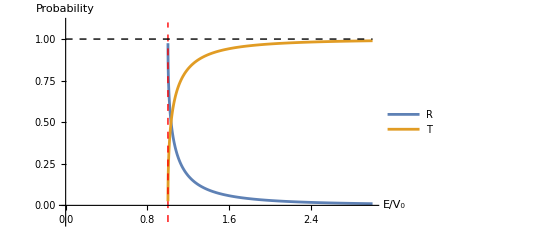

```mathematica
qmplt=Plot[{R,T},{e,0,3},PlotRange->{{0,3},{-0.1,1.1}},PlotLegends->{"R","T"},AxesLabel->{"E/V_0","Probability"},Epilog->{Red,Dashed,Line[{{1,-0.1},{1,1.1}}],Black,Dashed,Line[{{0,1},{3,1}}]}]
```

```mathematica
Export["qmplt.pdf",qmplt]
```

qmplt.pdf

## Afterword

```mathematica
Clear["Global`*"]
```

```mathematica
Solve[u ql - u0 ql ==√((u qr)^2+ω0^2)-u0 qr,qr]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{qr→(ql (u-u0) u0-√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2)},{qr→(ql (u-u0) u0+√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2)}}

```mathematica
qr=(ql (u-u0) u0+√((u-u0) (ql^2 u^2 (u-u0)-(u+u0) ω0^2)))/(u^2-u0^2);
```

```mathematica
ωp =u qr;ql=ω/(u-u0);Ω = √(ωp^2+ω0^2);ω=α ω0;u0 = γ u;
```

```mathematica
u=1;ω0=1;
```

```mathematica
{r,t}={b,c}/.Solve[{1+b==c,(u+u0)/(u-u0)*Abs[b]^2+(u ωp/Ω-u0)/(u-u0)*Abs[c]^2==1},{b,c}][[2]];
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

```mathematica
R=(u+u0)/(u-u0)Abs[r]^2;T=(u ωp/Ω-u0)/(u-u0)Abs[t]^2;
```

```mathematica
Manipulate[Plot[{R/.γ->g,T/.γ->g},{α,0,3},PlotRange->{{0,3},{-0.1,4}},PlotLegends->{"R","T"},AxesLabel->{"ω/ω_0", "Probability"},Epilog->{Red,Dashed,Line[{{√(1-g^2),-0.1},{√(1-g^2),1.1}}],Black,Dashed,Line[{{0,1},{3,1}}]}],{{g,-0.8,"u_0/u = "},-1,1}]
```

## Stuff for report

```mathematica
Clear["Global`*"]
```

```mathematica
vertical={ColorData[97,"ColorList"][[1]],Thick,Line[{{0,0},{0,1}}]};
```

```mathematica
energy={Red,Dashed,Line[{{-3,1.3},{3,1.3}}]};
```

```mathematica
potential={Black,Arrowheads[{-0.05,0.05}],Arrow[{{1,0},{1,1}}]};
```

```mathematica
text={Text[Style["V_0",16],{1.3,0.5}],Text[Style["E",16,Red],{-2.5,1.15}]};
```

```mathematica
arrowhead1={ColorData[97,"ColorList"][[1]],Thick,Arrowheads[{0.05}],Arrow[{{0,1},{3,1}}]};
```

```mathematica
arrowhead2={ColorData[97,"ColorList"][[1]],Thick,Arrowheads[{0.05}],Arrow[{{0,0},{-3,0}}]};
```

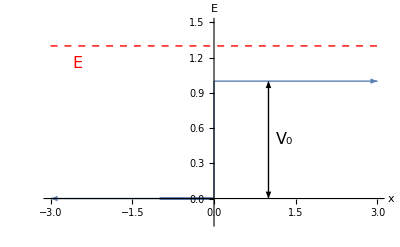

```mathematica
nrgplt=Plot[0,{x,-1,0},PlotRange->{{-3,3},{-0.2,1.5}},Ticks->None,AxesLabel->{"x","E"},Epilog->{vertical,energy,potential,text,arrowhead1,arrowhead2}]
```

```mathematica
Export["stepscattering.pdf",nrgplt]
```

stepscattering.pdf

```mathematica
Clear["Global`*"]
```

```mathematica
size=0.35;
```

```mathematica
d1={LightGray,Parallelogram[{0,0},{{1,0},{size,size}}]};
```

```mathematica
d2={Gray,Parallelogram[{0.5,0},{{0.5,0},{size,size}}]};
```

```mathematica
arrow={Red,Thickness[0.02],Arrowheads[{0.08}],Arrow[{{0.3,size/1.8},{0.5,size/1.8}}]};
```

```mathematica
bfield={Blue,Thickness[0.03],Arrowheads[{0.1}],Arrow[{{0.95,size/2},{0.95,size/0.9}}]};
```

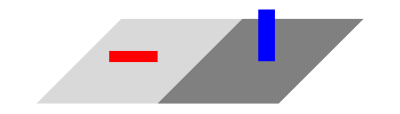

```mathematica
scatProb=Show[Graphics[{d1,d2,arrow,bfield}]]
```

```mathematica
Export["scatProb.pdf",scatProb]
```

scatProb.pdf

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]:=Tanh[5 x]+1
```

```mathematica
arrowhead1={ColorData[97,"ColorList"][[1]],Thick,Arrowheads[{0.05}],Arrow[{{2.9,f[2.9]},{3,f[3]}}]};
```

```mathematica
arrowhead2={ColorData[97,"ColorList"][[1]],Thick,Arrowheads[{0.05}],Arrow[{{-2.9,f[-2.9]},{-3,f[-3]}}]};
```

```mathematica
potential={Black,Arrowheads[{-0.05,0.05}],Arrow[{{2.5,0},{2.5,f[2.5]}}]};
```

```mathematica
energy={Red,Dashed,Line[{{-3,2.5},{3,2.5}}]};
```

```mathematica
text={Text[Style["V_0Tanh[β x] + V_0",16],{1.3,1}],Text[Style["E",16,Red],{-2.3,2.2}]};
```

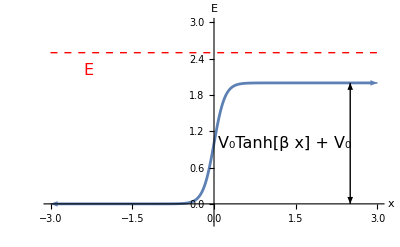

```mathematica
rosenmorse = Plot[f[x],{x,-2.9,2.9},PlotRange->{{-3,3},{-0.3,3}},Ticks->None,AxesLabel->{"x","E"},Epilog->{arrowhead1,arrowhead2,potential,energy,text}]
```

```mathematica
Export["rosenmorse.pdf",rosenmorse]
```

rosenmorse.pdf